# Calculations supporting A core-halo pattern of entropy creation in gravitational collapse, Wren (2018)

This notebook provides calculations supporting this paper, prepared for submission to MNRAS.

It is structured in line with the Appendices to Wren (2018), which cite this notebook.  All the paper’s Figures, including those in the main text, and its Table, are also generated by this notebook.

All equation and other references are to A core-halo pattern of entropy creation in gravitational collapse, Andrew J Wren (2018).

There is a supporting data file for this notebook, “Data for Entropy and gravitational collapse Wren 2018.m” which should be downloaded, and placed in the directory from which your Mathematica reads files.  The relevant parts of this notebook also provide (commented out) the code which generated this file.

Respond “Yes” when, on evaluation, the notebook asks to automatically evaluate all initialisation cells. 

The notebook takes around 10-20 minutes to run on a standard PC.

We assume throughout that,

```mathematica
$Assumptions=Subscript[k, J]>0&&σ>0&&V>0&&σ1>0&&κ>0&&-1≤cth≤1&&1≤cpsi≤1;
```

k_J, σ, V, and σ1 are defined in the paper.

A dummy variable κ is frequently used in order to help derive power series up to a given order in a set of k variables: every k variable then being paired with a κ, so, for example the magnitude k_1^2 becomes (κ k_1)^2. Series are then expanded up to a power of κ, which is the easiest way to expand up to a given total power of any product of k variables.  At the end of our calculations, κ is set to 1.

The variables cth and cpsi are defined in the part of this notebook relating to Appendix H.

Contents

Appendices B1 and B2
	Calculations for equations in Appendices B1 and B2
	Calculation of Figure 1
	Calculation of Figure B1

Appendix B3

Appendix C and Figure C1

Appendix F
	Quantities that occur in Eq. (F19)
	Evaluating Eqs. (F19) and (F20) to get Eq. (F21)
	
Appendix G
	Calculating the driving matrix (D̃)_1
	Calculating the vector ν
	Constructing the matrix M
	Calculating the result (γ̃)_a
	
Appendix H1-3
	Appendix H1: Calculating the numerical factor for Eq. (44)
	Appendix H1: Calculating Table H1
	Appendix H1: Variant of total net entropy creation with numerical integration constraining only two of k1, k2, and kp to be less than 1
	Appendix H2: calculating the distribution over space plots for Figure 2
	Appendix H2: confirming the core and the halo balance at leading order
	Appendix H3: calculating the next-to-leading order distribution over space plots for Figure H1
	Appendix H3: confirming the next-to-leading order distribution over space integrates to the total net entropy creation

Appendix H4
	Variant of Appendix F approach
		Variants of quantities that occur in Eq. (F19)
		Variant evaluation of Eqs. (F19) and (F20) to get Eq. (F22)
	Variant of Appendix G approach
		Calculating the variant driving matrix (D̃)_1
		Calculating the variant of the vector ν
		Calculating the variant result (γ̃)_a
	Preparing and doing the variant numerical integration
	Calculating next-to-leading order distribution over space plots for the limit σ_1→0, and plotting Figure H2

Creating the data file
	
Initialisation cells

## Appendices B1 and B2

## Calculations for equations in Appendices B1 and B2

The next lines are the formula for approximating Z given in Eq. (B3), including its expansion to four terms, both only for Im[z]>0:

```mathematica
Zapprox[z_,numberofZterms_]:=-Sum[((j-1/2)!)/(√π*z^(2*j+1)),{j,0,numberofZterms-1}]
```

```mathematica
Zapprox[z,4]
```

-15/(8 z^7)-3/(4 z^5)-1/(2 z^3)-1/z

This implies, via Eq. (35) the following formula for P(k,ω), again only for Im[z]>0:

```mathematica
Papprox[k_,ω_,numberofPterms_]:=1+ω/(√2*σ*k)*Zapprox[ω/(√2*σ*k),numberofPterms+1]
```

```mathematica
Expand[Papprox[k,ω,4]]
```

-(105 k^8 σ^8)/ω^8-(15 k^6 σ^6)/ω^6-(3 k^4 σ^4)/ω^4-(k^2 σ^2)/ω^2

Now check the formula for the zero of the dispersion relation k^2=k_J^2 P(k,ⅈη), as given in Eq. (B5),

```mathematica
η=Subscript[k, J] σ-(3σ k^2)/(2 Subscript[k, J])+(15σ k^4)/(8 Subscript[k, J]^3)-(147σ k^6)/(16 Subscript[k, J]^5)+(9531σ k^8)/(128 Subscript[k, J]^7);
```

Confirm that this formula for η satisfies the dispersion relation up to and including order 9 in k:

```mathematica
Series[k^2-Subscript[k, J]^2 Papprox[k,ⅈ*η,4],{k,0,9}]
```

O[k]^10

## Calculation of Figure 1

This uses the method described in the paragraph containing Eq. (B6), which is expressed in the next function.  Here, and for other figures, we have chosen units so that σ=k_J=1

```mathematica
Z[z_]:=Which[Im[z]≥1,ContinuedFractionK[If[n==1,z,-1/2 (-1+n) (-3+2 n)],-z^2-3/2+2 n,{n,1,20}],-1<Im[z]<1,ⅈ*√π*Exp[-z^2]*(1+Erf[ⅈ*z]),Im[z]≤-1,2*ⅈ*√π*Exp[-z^2]+Conjugate[ContinuedFractionK[If[n==1,Conjugate[z],-1/2 (-1+n) (-3+2 n)],-Conjugate[z]^2-3/2+2 n,{n,1,20}]],True,"Error"]
```

```mathematica
P[k_,ω_]:=1+ω/(√2*k)*Z[ω/(√2*k)]
```

Numerically find a zero for the dispersion equation:

```mathematica
positiveimaginarydispersionzero[k_]:=Im[FindRoot[P[k,ω]==k^2,{ω,ⅈ}][[1,2]]]
```

Produce Figure 1:

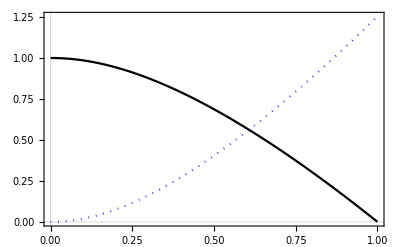

```mathematica
Figure1=Plot[{positiveimaginarydispersionzero[k],(1-k^2-positiveimaginarydispersionzero[k]^2)/positiveimaginarydispersionzero[k]},{k,0,1},FrameLabel->{MaTeX["\\sfrac{k}{k_\\text{J}}",Magnification->1.25],""},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->{Black,{Blue,Dotted}},PlotPoints->1000,PlotLegends->{MaTeX["\\sfrac{\\eta(k)}{k_\\text{J}\\sigma}",Magnification->1.25*1.3],MaTeX["\\frac{\\sigma^2\\left(k_\\text{J}^2-k^2\\right)-\\eta(k)^2}{k_\\text{J}\\eta(k)\\sigma}",Magnification->0.9*1.3]}]
```

If uncommented, export Figure 1 as a pdf file:

```mathematica
(*Export["EGCFigure1.pdf",Figure1];*)
```

## Calculation of Figure B1

Calculate the left plot of Figure B1, using the previous two sections of this notebook:

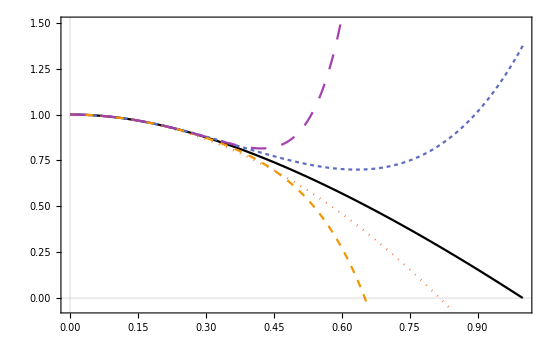

```mathematica
FigureB1left=Plot[{positiveimaginarydispersionzero[k],1-3/2 k^2,1-3/2 k^2+15/8 k^4,1-3/2 k^2+15/8 k^4-147/16 k^6,1-3/2 k^2+15/8 k^4-147/16 k^6+9531/128 k^8},{k,0,1},FrameLabel->{MaTeX["\\sfrac{k}{k_\\text{J}}",Magnification->2],MaTeX["\\sfrac{\\eta(k)}{k_\\text{J}\\sigma}",Magnification->2]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->ps8,PlotPoints->1000,ImageSize->554,PlotRange->{Full,{-0.05,1.5}},ImagePadding->{{Automatic,Automatic},{Automatic,None}}]
```

The following (which takes some time to evaluate) calculates the right plot of Figure B1, again using the previous two sections of this notebook:

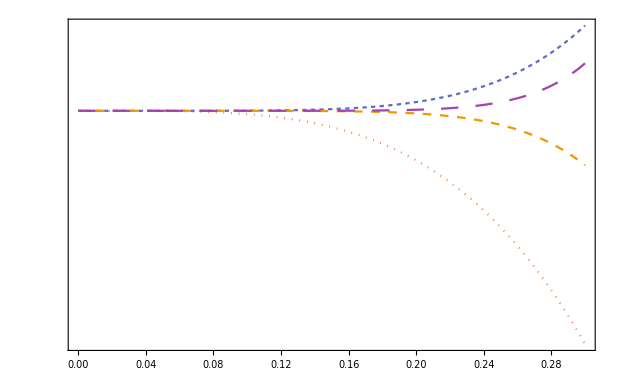

```mathematica
FigureB1right=LogPlot[{(1-3/2 k^2)/positiveimaginarydispersionzero[k],(1-3/2 k^2+15/8 k^4)/positiveimaginarydispersionzero[k],(1-3/2 k^2+15/8 k^4-147/16 k^6)/positiveimaginarydispersionzero[k],(1-3/2 k^2+15/8 k^4-147/16 k^6+9531/128 k^8)/positiveimaginarydispersionzero[k]},{k,0,0.3},FrameLabel->{MaTeX["\\quad\\sfrac{k}{k_\\text{J}}",Magnification->2],MaTeX["\\sfrac{\\text{Series}}{\\text{Exact}}",Magnification->2]},BaseStyle->texStyle,FrameStyle->BlackFrame,RotateLabel->False,PlotStyle->ps8log,PlotPoints->1000,ImageSize->620,GridLines->{{0},{1-1 10^-2,1-1 10^-3,1,1+1 10^-3}},PlotRange->Full,FrameTicks->laxsticks,ImagePadding->{{Automatic,Automatic},{Automatic,None}}]
```

Combine the above to make the full figure:

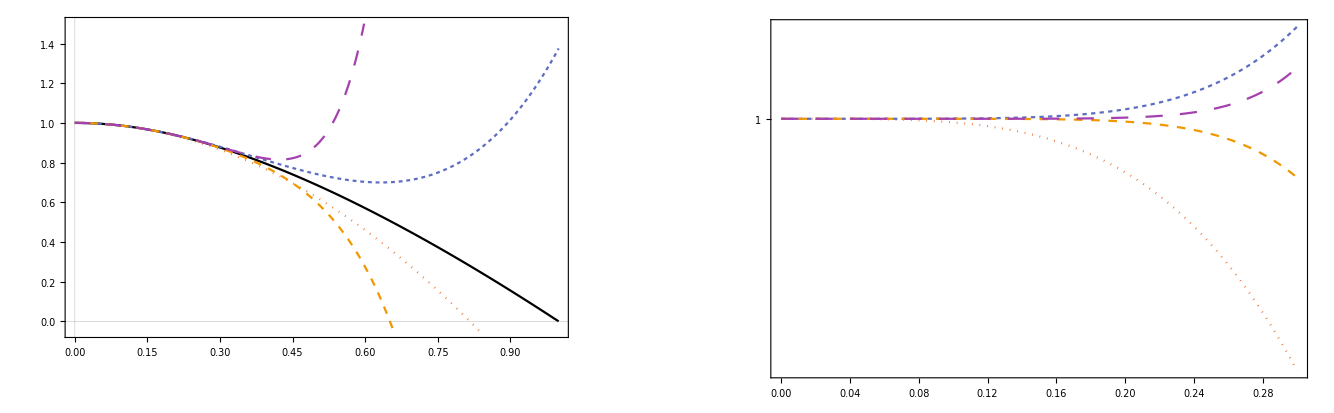

```mathematica
FigureB1=Legended[GraphicsRow[{FigureB1left,FigureB1right},Alignment->Top],Placed[LineLegend[ps8,pl,LegendLayout->"Row"],Below]]
```

If uncommented, export Figure B1 as a pdf file :

```mathematica
(*Export["EGCFigureB1.pdf",FigureB1];*)
```

## Appendix B3

This section of the notebook does the calculations referred to after Eq. (B12), checking the formulae for the size and argument of the dispersion zeros given in Eqs. (B11) and (B12) respectively

Define a function which numerically finds dispersion relation zeros with negative imaginary parts:

```mathematica
negativeimaginarydispersionzero[k_,start_]:=FindRoot[P[k,ω]==k^2,{ω,start*(1-ⅈ)/(√2)}][[1,2]]
```

Using this, define a function which generates a set of such zeros, using a range of start points for the numerical calculation.  (The function only admits solutions which satisfy the dispersion relation sufficiently accurately, and suppresses error messages which will be associated with rejected solutions.  It also rounds solutions to decimalplaces decimal places, and de-duplicates.)

```mathematica
setofzeros[k_,begintstartrange_,endstartrange_,decimalplaces_]:=Quiet[SortBy[DeleteDuplicatesBy[Cases[Table[If[Abs[P[k,result=negativeimaginarydispersionzero[k,start]]-k^2]<=10^-decimalplaces,Chop[result]],{start,begintstartrange,endstartrange,10^-decimalplaces}],Except[Null]],(Round[#,10^-decimalplaces])&],Re]]
```

Uncommented, the next line was originally used (taking an hour or two on a standard PC) to calculate (and export) zeros ω in the range 10< |ω|<11 for k=0.1 k_J and k=0.01 k_J...

```mathematica
(*B3data1=Cases[setofzeros[0.1,9,12,4],ω_/;10<Abs[ω]<11];B3data2=Cases[setofzeros[0.01,9,12,5],ω_/;10<Abs[ω]<11];B3data={B3data1,B3data2};Export["Appendix B3 data.m",B3data];*)
```

...but it can also be more quickly imported from a data file comprising this and other data, using the next line

```mathematica
B3data=<<"Data for Entropy and gravitational collapse Wren 2018.m"[[1]];
```

From the numerical solutions for the dispersion relation, count the number of zeros ω in the range 10< |ω|<11, for, respectively, k=0.1 k_J and k=0.01 k_J:

```mathematica
Map[Length,B3data]
```

{168,16712}

Define a function counting the number of zeros according to the approximation in Eq. (B11):

```mathematica
nozerosEqB10[k_,ω1_,ω2_]:=(Ceiling[(2 Max[ω1,ω2]^2-3 k^2 π)/(8 k^2 π)]-1)-(Floor[(2 Min[ω1,ω2]^2-3 k^2 π)/(8 k^2 π)]+1)+1
```

Count the number of zeros predicted by Eq. (B11) for, respectively, k=0.1 k_J and k=0.01 k_J:

```mathematica
nozerosEqB10[{0.1,0.01},10,11]
```

{167,16711}

This is very close to the numerically-calculated values derived just above.

Calculate the maximum deviation from the diagonal from the numerical solutions for the dispersion zeros:

```mathematica
(paddedscientificform[(Arg[MaximalBy[#,Arg]][[1]]-(-π/4)),3])&/@B3data
```

{ 1.01×10^-3, 1.70×10^-5}

To calculate the maximum deviation from the diagonal using the approximation in Eq. (B12), first find the index number n for the first zero ω in the range 10< |ω|<11:

```mathematica
nfirstzero=(Floor[(2*10^2-3 #^2 π)/(8 #^2 π)]+1)&/@{0.1,0.01};
```

Then calculate the deviation from the diagonal for those n, as predicted by Eq. (B12):

```mathematica
deviationB11[k_,n_]:=1/(4 π (n+3/8)) Log[(2 π √(2n+3/4))/k^2]
```

```mathematica
paddedscientificform[{deviationB11[0.1,nfirstzero[[1]]],deviationB11[0.01,nfirstzero[[2]]]},3]
```

{ 1.01×10^-3, 1.70×10^-5}

To this number of significant figures, it is the same as the numerically-calculated values derived just above.

## Appendix C and Figure C1

The following function gives the essence of the number density, as set out in Eq. (C2),

```mathematica
numberdensity[r_]:=(Sin[r]-r Cos[r])/(2 π^2 r^3)
```

Plot Figure C1 (Left):

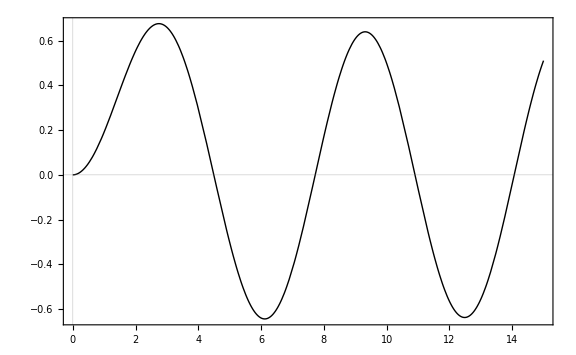

```mathematica
densitybyshell=Plot[numberdensity[r] 4 π r^2,{r,0,15},GridLines->{{0},{0}},PlotRange->Full,PlotStyle->{Thin,Black},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["4\\pi r^2\\,\\frac{n_{1,\\text{acg}}\\left(k_{\\text{J}}\\beta\\, r\\right)}{k_{\\text{J}}\\beta\\,\\text{e}^{k_\\text{J}\\sigma\\, t}}",Magnification->1.25]},RotateLabel->False]
```

Plot Figure C1 (Right):

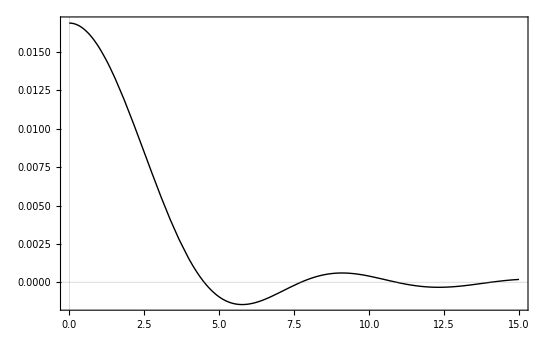

```mathematica
densitybyvolume=Plot[numberdensity[r],{r,0,15},GridLines->{{0},{0}},PlotRange->Full,PlotStyle->{Thin,Black},ImageSize->550,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\frac{n_{1,\\text{acg}}\\left(k_{\\text{J}}\\beta\\, r\\right)}{\\left(k_{\\text{J}}\\beta\\right)^3\\text{e}^{k_\\text{J}\\sigma\\, t}}",Magnification->1.25]},RotateLabel->False]
```

Combine these into  Figure C1:

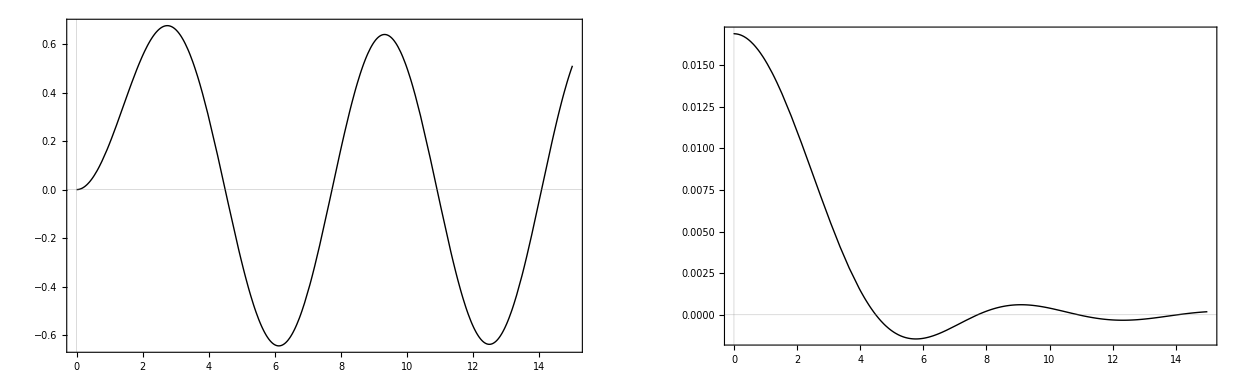

```mathematica
FigureC1=GraphicsRow[{densitybyshell,densitybyvolume},BaselinePosition->Top]
```

If uncommented, export Figure C1 as a pdf file :

```mathematica
(*Export["EGCFigureC1.pdf",FigureC1];*)
```

## Appendix F

This part calculates a series expansion for I_D_1, see Eq. (F19), for use in Eq. (F20), and from that then derives Eq. (F21) for γ_a(k_1,v_1,k_2,t).

Aside, which may safely be ignored: We do all power series expansions initially to order 8 to be sure that no terms are missed, in particular in calculating I_D_1, which as a sum of terms might see cancellations which increase its leading order.  In fact, this does not occur and the leading order of I_D_1 is zero.  It can be seen from adjusting this this notebook that calculating all expressions initially to order 4 (but no less) would be sufficient.

## Quantities that occur in Eq. (F19)

Ensure we do not define η_1, η_2 and ηE=η_1+η_1 until later:

```mathematica
Clear[η1];Clear[η2];Clear[ηE];
```

Y(k_1,ⅈ η_1) and Y(k_2,ⅈ η_2) are written using the dispersion relation:

```mathematica
Y11=((κ k1)^2-Subscript[k, J]^2)/(Subscript[k, J]^2 ⅈ η1);Y22=((κ k2)^2-Subscript[k, J]^2)/(Subscript[k, J]^2 ⅈ η2);
```

From these, we get P(k_1,ⅈ η_1) and P(k_2,ⅈ η_2):

```mathematica
P11=1+ⅈ η1 Y11;P22=1+ⅈ η2 Y22;
```

Also define expressions for the derivative of the Y and P functions with respect to the ω variables, which can be found using the expression mentioned after Eq. (B17),

```mathematica
dY11=-1/(κ k1 σ)^2 (1+ⅈ η1 Y11);dY22=-1/(κ k2 σ)^2 (1+ⅈ η2 Y22);dP11=Y11+ⅈ η1 dY11;dP22=Y22+ⅈ η2 dY22;
```

Derive a series expansion for the function Y(k,ω,k_+,ω_+) from Eq. (F17), writing kppa and kppe for the parts of k_+ respectively parallel and perpendicular to k, and ωp for ω_+.  The easiest way to do this is to use Mathematica’s Expectation function to evaluate the Gaussian “moments”, using an approach similar to that which derives the series for Eq. (B3).

```mathematica
Ydouble=Collect[Expand[Expectation[Normal[Series[1/((κ k) vpa-ω) 1/((κ kppa) vpa+(κ kppe) vpe-ωp),{κ,0,8}]],{vpa,vpe}\[Distributed]MultinormalDistribution[{0,0},σ^2 IdentityMatrix[2]]]],{κ}];
```

We will also need its derivative with respect to ω:

```mathematica
dYdouble=D[Ydouble,ω];
```

Write Y(k_1,ⅈ η_1,k_+,ⅈ E) and Y(k_2,ⅈ η_2,k_+,ⅈ E), and also related derivatives:

```mathematica
Y11pE=Simplify[Ydouble//.{k->k1,ω->ⅈ η1,kppa->k1dotkp/k1,kppe->√(kp^2-kppa^2),ωp->ⅈ ηE}];
```

```mathematica
Y22pE=Simplify[Ydouble//.{k->k2,ω->ⅈ η2,kppa->k2dotkp/k2,kppe->√(kp^2-kppa^2),ωp->ⅈ ηE}];
```

```mathematica
dY11pE=Simplify[dYdouble//.{k->k1,ω->ⅈ η1,kppa->k1dotkp/k1,kppe->√(kp^2-kppa^2),ωp->ⅈ ηE}];
```

```mathematica
dY22pE=Simplify[dYdouble//.{k->k2,ω->ⅈ η2,kppa->k2dotkp/k2,kppe->√(kp^2-kppa^2),ωp->ⅈ ηE}];
```

Express P(k_1,ⅈ η_1,k_+,ⅈ E) and P(k_2,ⅈ η_2,k_+,ⅈ E) from Eq. (F17) in terms of Y functions by separating fractions in their integrals, and we can also find related derivatives:

```mathematica
P11pE=Y11+ⅈ ηE Y11pE;P22pE=Y22+ⅈ ηE Y22pE;dP11pE=dY11+ⅈ ηE dY11pE;dP22pE=dY22+ⅈ ηE dY22pE;
```

We also need Y(k_+,ⅈ E) and P(k_+,ⅈ E):

```mathematica
YpE=Simplify[Normal[Series[-1/(ⅈ ηE)-(σ^2 (κ kp)^2)/(ⅈ ηE)^3-(3 σ^4 (κ kp)^4)/(ⅈ ηE)^5-(15 σ^6 (κ kp)^6)/(ⅈ ηE)^7-(105 σ^8 (κ kp)^8)/(ⅈ ηE)^9,{κ,0,8}]]];PpE=1+ⅈ ηE YpE;
```

We now define expressions for η_1, η_2 and ηE.  Had we done so earlier, some of the above evaluations would have been much slower.  Use Eq. (B5) to define η_1 and η_2:

```mathematica
η1=Subscript[k, J] σ-(3 σ (κ k1)^2)/(2 Subscript[k, J])+(15 σ (κ k1)^4)/(8 Subscript[k, J]^3)-(147 σ (κ k1)^6)/(16 Subscript[k, J]^5)+(9531 σ (κ k1)^8)/(128 Subscript[k, J]^7);η2=Subscript[k, J] σ-(3 σ (κ k2)^2)/(2 Subscript[k, J])+(15 σ (κ k2)^4)/(8 Subscript[k, J]^3)-(147 σ (κ k2)^6)/(16 Subscript[k, J]^5)+(9531 σ (κ k2)^8)/(128 Subscript[k, J]^7);ηE=η1+η2;
```

We also define expressions for q̄(k_1) and q̄(k_2),

```mathematica
q1=-Subscript[k, J]^2/(V (Subscript[k, J]^2-(κ k1)^2));q2=-Subscript[k, J]^2/(V (Subscript[k, J]^2-(κ k2)^2));
```

## Evaluating Eqs. (F19) and (F20) to get Eq. (F22)

This then enables us to write a series expansion for Eq. (F19) as

```mathematica
ID1=Normal[Series[(((Subscript[k, J]^2 P11)/(κ k1)^2 (Y22pE+(Subscript[k, J]^2 P22pE YpE)/((κ kp)^2-Subscript[k, J]^2 PpE))+(Subscript[k, J]^2 κ^2 k1dotkp P11 Y22 YpE)/((κ k1)^2 ((κ kp)^2-Subscript[k, J]^2 PpE)) V q2+(Subscript[k, J]^2 σ^2 κ^2 k1dotk2 Y22)/(κ k2)^2 (dY11pE+(Subscript[k, J]^2 YpE)/((κ kp)^2-Subscript[k, J]^2 PpE) dP11pE) (V q2+1))+((Subscript[k, J]^2 P22)/(κ k2)^2 (Y11pE+(Subscript[k, J]^2 P11pE YpE)/((κ kp)^2-Subscript[k, J]^2 PpE))+(Subscript[k, J]^2 κ^2 k2dotkp P22 Y11 YpE)/((κ k2)^2 ((κ kp)^2-Subscript[k, J]^2 PpE)) V q1+(Subscript[k, J]^2 σ^2 κ^2 k1dotk2 Y11)/(κ k1)^2 (dY22pE+(Subscript[k, J]^2 YpE)/((κ kp)^2-Subscript[k, J]^2 PpE) dP22pE) (V q1+1))),{κ,0,8}]];
```

The remaining factors in Eq. (F20), other than the Maxwellian and the time exponential, can be written as

```mathematica
F20remaining=Simplify[-((κ k1dotv1)/(κ k1dotv1-ⅈ η1) ((Subscript[k, J]^2 η1 η2 σ^4 (κ k2)^2)/((σ^2 (Subscript[k, J]^2-(κ k1)^2)-η1^2) (σ^2 (Subscript[k, J]^2-(κ k2)^2)-η2^2))))];
```

where k1dotv1 is k_1·v_1.  The right-hand side of Eq. (F22), other than the Maxwellian and the time exponential, can therefore be written as the following:

```mathematica
F22expression=Collect[Series[F20remaining ID1,{κ,0,2}]//.{k2dotkp->kp^2-k1dotkp,k1dotk2->k1dotkp-k1^2,k2^2->kp^2+k1^2-2 k1dotkp},{κ,k1dotv1 },Simplify];
```

Set the dummy variable κ to 1 to get the final expression:

```mathematica
F22expressionNoκ=F22expression/.{κ->1}
```

k1dotv1^2/(4 k1^2 σ^2)-k1dotv1^4/(4 k1^2 σ^4 k_J^2)+(k1dotv1^2 (4 k1dotkp^2+20 k1^2 kp^2-15 k1dotkp kp^2+6 kp^4))/(12 k1^2 kp^2 σ^2 k_J^2)-(ⅈ k1dotv1^3)/(4 k1^2 σ^3 k_J)+(ⅈ k1dotv1 (8 k1dotkp^2+31 k1^2 kp^2-30 k1dotkp kp^2+12 kp^4))/(24 k1^2 kp^2 σ k_J)+(ⅈ k1dotv1 k_J)/(4 k1^2 σ)

The above expression is the factor on the right-hand side of  Eq. (F22), in braces, which when multiplied by the Maxwellian and the time exponential, as set out in that equation, gives γ_a(k_1,v_1,k_2,t).

## Appendix G

## Calculating the driving matrix (D̃)_1

We start by defining two more series approximations using the function Zapprox from above,

```mathematica
Yapprox[p_,ω_,κ_,numberofYterms_]:=1/(κ √(2 p.p) σ) Zapprox[ω/(κ √(2 p.p) σ),numberofYterms]
```

```mathematica
Papprox2[p_,ω_,κ_,numberofPterms_]:=1+ω Yapprox[p,ω,κ,numberofPterms+1]
```

From Eq. (F3), neglecting terms of higher order in V^-1, and leaving aside Maxwellian factors, we have the driving term,

```mathematica
D1tilde[k1_,v1_,k2_,v2_,kp_]:=(ⅈ Subscript[k, J]^2 kp.v1)/(kp.kp) intf1[kp] V q[k2]+(ⅈ Subscript[k, J]^2)/(k2.k2) σ^2 k2.df1[kp,v1] (V q[k2]+1)+(ⅈ Subscript[k, J]^2 k1.v1)/(k1.k1) f1[kp,v2]+(ⅈ Subscript[k, J]^2 kp.v2)/(kp.kp) intf1[kp] V q[k1]+(ⅈ Subscript[k, J]^2)/(k1.k1) σ^2 k1.df1[kp,v2] (V q[k1]+1)+(ⅈ Subscript[k, J]^2 k2.v2)/(k2.k2) f1[kp,v1]
```

where f1, intf1, and df1 are, respectively, the function OverTilde[f^-]_1, and its integral and derivative with respect to velocity, all implicitly curtailed at some suitable power in k.  From Eq. (37), we have, leaving aside the Maxwellian factor, a series expansion for OverTilde[f^-]_1(p,v,ω) as

```mathematica
FullSimplify[((Normal[Series[-ⅈ/(κ p.v-ω)-(ⅈ Subscript[k, J]^2 κ p.v Yapprox[p,ω,κ,4])/((κ p.v-ω)(κ^2 p.p-Subscript[k, J]^2 Papprox2[p,ω,κ,3])),{κ,0,4}]])/.κ->1)]
```

1/(ω^5 p.p (ω^2+σ^2 k_J^2)^3)ⅈ (-p.v (ω+p.v) (ω^2-ω p.v+(p.v)^2) (ω^2+p.v (ω+p.v)) k_J^2 (ω^2+σ^2 k_J^2)^2+3 σ^4 (p.p)^2 p.v (ω+p.v) k_J^2 (-ω^4+4 σ^2 ω^2 k_J^2+2 σ^4 k_J^4)+p.p (ω^2+σ^2 k_J^2) (ω^8+ω^4 p.v (ω+p.v) (ω^2+(p.v)^2)+σ^2 ω^2 (2 ω^4+p.v (ω+p.v) (ω^2+(p.v)^2)) k_J^2+σ^4 (ω^4+3 p.v (ω+p.v) (ω^2+(p.v)^2)) k_J^4))

We use this to define the function,

```mathematica
f1[p_,v_]:=1/(ω^5 p.p (ω^2+σ^2 Subscript[k, J]^2)^3)ⅈ (-p.v (ω+p.v) (ω^2-ω p.v+(p.v)^2) (ω^2+p.v (ω+p.v)) Subscript[k, J]^2 (ω^2+σ^2 Subscript[k, J]^2)^2+3 σ^4 (p.p)^2 p.v (ω+p.v) Subscript[k, J]^2 (-ω^4+4 σ^2 ω^2 Subscript[k, J]^2+2 σ^4 Subscript[k, J]^4)+p.p (ω^2+σ^2 Subscript[k, J]^2) (ω^8+ω^4 p.v (ω+p.v) (ω^2+(p.v)^2)+σ^2 ω^2 (2 ω^4+p.v (ω+p.v) (ω^2+(p.v)^2)) Subscript[k, J]^2+σ^4 (ω^4+3 p.v (ω+p.v) (ω^2+(p.v)^2)) Subscript[k, J]^4))
```

Note that use of p as the momentum variable is to avoid a variable k and the constant k_J getting confused by Mathematica. For the same reason k must not be used as a variable to which f1 is applied, although, for example k1 and k2, as in the definition of D1tilde do not cause any such problems.

Similarly, we have the integral of OverTilde[f^-]_1(p,v,ω) with respect to v, gives a series, leaving aside its Maxwellian factor,

```mathematica
FullSimplify[((Normal[Series[-ⅈ Yapprox[p,ω,κ,4]-(ⅈ Subscript[k, J]^2 Papprox2[p,ω,κ,3] Yapprox[p,ω,κ,4])/(κ^2 p.p-Subscript[k, J]^2 Papprox2[p,ω,κ,3]),{κ,0,4}]])/.κ->1)]
```

(ⅈ (σ^2 ω^2 p.p (ω^2-2 σ^2 k_J^2) (ω^2+σ^2 k_J^2)+ω^4 (ω^2+σ^2 k_J^2)^2+3 σ^4 (p.p)^2 (ω^4-4 σ^2 ω^2 k_J^2-2 σ^4 k_J^4)))/((ω^3+σ^2 ω k_J^2)^3)

We use this to define the function,

```mathematica
intf1[p_]:=1/((ω^3+σ^2 ω Subscript[k, J]^2)^3)ⅈ (σ^2 ω^2 p.p (ω^2-2 σ^2 Subscript[k, J]^2) (ω^2+σ^2 Subscript[k, J]^2)+ω^4 (ω^2+σ^2 Subscript[k, J]^2)^2+3 σ^4 (p.p)^2 (ω^4-4 σ^2 ω^2 Subscript[k, J]^2-2 σ^4 Subscript[k, J]^4))
```

and the derivative of OverTilde[f^-]_1(p,v,ω) with respect to v, gives a series, leaving aside its Maxwellian factor,

```mathematica
Simplify[((Normal[Series[(ⅈ κ p)/(κ p.v-ω)^2+(ⅈ v/σ^2)/(κ p.v-ω)-(ⅈ Subscript[k, J]^2 Yapprox[p,ω,κ,4])/((κ p.v-ω)(κ^2 p.p-Subscript[k, J]^2 Papprox2[p,ω,κ,3]))(κ p-(κ p.v v)/σ^2-(κ^2 p.v p)/(κ p.v-ω)),{κ,0,4}]])/.κ->1)]
```

1/(σ^2 ω^5 p.p (ω^2+σ^2 k_J^2)^3)ⅈ (-(p σ^2 ω^5+ω^4 (2 p σ^2-v ω) p.v+ω^3 (3 p σ^2-v ω) (p.v)^2+ω^2 (4 p σ^2-v ω) (p.v)^3+ω (5 p σ^2-v ω) (p.v)^4+(6 p σ^2-v ω) (p.v)^5-v (p.v)^6) k_J^2 (ω^2+σ^2 k_J^2)^2+3 σ^4 (p.p)^2 (p σ^2 ω+(2 p σ^2-v ω) p.v-v (p.v)^2) k_J^2 (-ω^4+4 σ^2 ω^2 k_J^2+2 σ^4 k_J^4)-p.p (ω^2+σ^2 k_J^2) (ω^7 (-p σ^2+v ω)+σ^2 ω^5 (-p σ^2+2 v ω) k_J^2+σ^4 ω^3 (-3 p σ^2+v ω) k_J^4+ω^2 (-2 p σ^2+v ω) p.v (ω^4+σ^2 ω^2 k_J^2+3 σ^4 k_J^4)+ω (-3 p σ^2+v ω) (p.v)^2 (ω^4+σ^2 ω^2 k_J^2+3 σ^4 k_J^4)-(4 p σ^2-v ω) (p.v)^3 (ω^4+σ^2 ω^2 k_J^2+3 σ^4 k_J^4)+v (p.v)^4 (ω^4+σ^2 ω^2 k_J^2+3 σ^4 k_J^4)))

We use this to define the function,

```mathematica
df1[p_,v_]:=1/(σ^2 ω^5 p.p (ω^2+σ^2 Subscript[k, J]^2)^3)ⅈ (-(p σ^2 ω^5+ω^4 (2 p σ^2-v ω) p.v+ω^3 (3 p σ^2-v ω) (p.v)^2+ω^2 (4 p σ^2-v ω) (p.v)^3+ω (5 p σ^2-v ω) (p.v)^4+(6 p σ^2-v ω) (p.v)^5-v (p.v)^6) Subscript[k, J]^2 (ω^2+σ^2 Subscript[k, J]^2)^2+3 σ^4 (p.p)^2 (p σ^2 ω+(2 p σ^2-v ω) p.v-v (p.v)^2) Subscript[k, J]^2 (-ω^4+4 σ^2 ω^2 Subscript[k, J]^2+2 σ^4 Subscript[k, J]^4)-p.p (ω^2+σ^2 Subscript[k, J]^2) (ω^7 (-p σ^2+v ω)+σ^2 ω^5 (-p σ^2+2 v ω) Subscript[k, J]^2+σ^4 ω^3 (-3 p σ^2+v ω) Subscript[k, J]^4+ω^2 (-2 p σ^2+v ω) p.v (ω^4+σ^2 ω^2 Subscript[k, J]^2+3 σ^4 Subscript[k, J]^4)+ω (-3 p σ^2+v ω) (p.v)^2 (ω^4+σ^2 ω^2 Subscript[k, J]^2+3 σ^4 Subscript[k, J]^4)-(4 p σ^2-v ω) (p.v)^3 (ω^4+σ^2 ω^2 Subscript[k, J]^2+3 σ^4 Subscript[k, J]^4)+v (p.v)^4 (ω^4+σ^2 ω^2 Subscript[k, J]^2+3 σ^4 Subscript[k, J]^4)))
```

while, from Eq. (41), we have, neglecting terms of higher order in V^-1, a series expansion up to order p^4,

```mathematica
q[p_]:=-1/V-(p.p)/(Subscript[k, J]^2 V)-(p.p)^2/(Subscript[k, J]^4 V)
```

which gives us all the functions making up D1tilde.

## Calculating the vector ν (nu)

From the definition of ν^(j)(k_1,k_2) in Eq. (G4), we need a factor,

```mathematica
G4factor[k1_,v1_,k2_,v2_]:=1+(k1.v1+k2.v2)/ω+((k1.v1+k2.v2)/ω)^2+((k1.v1+k2.v2)/ω)^3+((k1.v1+k2.v2)/ω)^4
```

Eq. (G10) defines  the vector ν (nu). Its first component is μ^(0) which is 0.  The second, fourth and sixth components are given by ν^(j)(k_1,k_2) for j=1,2,3.  The third, fifth and seventh are similarly ν^(j)(k_2,k_1).We write k_1 and k_2 in co-ordinate terms with their moduli k1 and k2, and the angle θ, which  k_2 makes to k_1; and we also now introduce the dummy variable κ.  Calculating ν takes less than two minutes on a standard PC:

```mathematica
ν=Join[{0},Flatten[Table[{term=Normal[Series[Expectation[ⅈ(κ k1 v1x)^j D1tilde[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0},{κ k1+κ k2 Cos[θ],κ k2 Sin[θ],0}] G4factor[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0}],{v1x,v1y,v2x,v2y}\[Distributed]MultinormalDistribution[{0,0,0,0},σ^2 IdentityMatrix[4]]],{κ,0,3}]],term/.{k1->k2,k2->k1,θ->-θ}},{j,1,3}]]];
```

## Constructing the matrix M

We construct M row by row from the relevant equations, Eqs. (G1), (G5)-(G7).

From Eq. (G1),

```mathematica
M0row={0,1,1,0,0,0,0};
```

From Eq. (G5),

```mathematica
M1arow=- Subscript[k, J]^2 σ^2 {(1+(3  κ^2 k1^2 σ^2)/ω^2),
1/ω (1+(3  κ^2 k2^2 σ^2)/ω^2),(1/ω+(9  κ^2 k1^2 σ^2)/ω^3),
1/ω (2/ω),1/ω^2,
1/ω (3/ω^2),1/ω^3};
```

and, with k_1 and k_2 swapped,

```mathematica
M1brow=- Subscript[k, J]^2 σ^2 {(1+(3  κ^2 k2^2 σ^2)/ω^2),
(1/ω+(9  κ^2 k2^2 σ^2)/ω^3),1/ω (1+(3  κ^2 k1^2 σ^2)/ω^2),
1/ω^2,1/ω (2/ω),
1/ω^3,1/ω (3/ω^2)};
```

From Eq. (G6),

```mathematica
M2arow=- Subscript[k, J]^2 σ^2 {(3  κ^2 k1^2 σ^2)/ω,
0,(6  κ^2 k1^2 σ^2)/ω^2,
1/ω (1),0,
1/ω (2/ω),0};
```

and, with k_1 and k_2 swapped,

```mathematica
M2brow=- Subscript[k, J]^2 σ^2 {(3  κ^2 k2^2 σ^2)/ω,
(6  κ^2 k2^2 σ^2)/ω^2,0,
0,1/ω (1),
0,1/ω (2/ω)};
```

From Eq. (G7),

```mathematica
M3arow=- Subscript[k, J]^2 σ^2 {3  κ^2 k1^2 σ^2,
0,(3  κ^2 k1^2 σ^2)/ω,
0,0,
1/ω (1),0};
```

and, with k_1 and k_2 swapped,

```mathematica
M3brow=- Subscript[k, J]^2 σ^2 {3  κ^2 k2^2 σ^2,
(3  κ^2 k2^2 σ^2)/ω,0,
0,0,
0,1/ω (1)};
```

We then have,

```mathematica
M=Simplify[{M0row,M1arow,M1brow,M2arow,M2brow,M3arow,M3brow}];
```

## Calculating the result, γ_a

For Eq. (G11), we have, cutting off higher powers of κ,

```mathematica
LInverse=Normal[Series[Inverse[ω IdentityMatrix[7]-M],{κ,0,3}]];
```

We now need to construct Γ and substitute it back into Eq. (G3). We start by writing the coefficients of the Γ matrices up to sufficient order in κ,

```mathematica
Γcoefficients=-(Subscript[k, J]^2 v1x)/(κ k1) {1+(κ k1 v1x)/ω+((κ k1 v1x)/ω)^2+((κ k1 v1x)/ω)^3,0,1/ω+(2 κ k1 v1x)/ω^2+(3 (κ k1 v1x)^2)/ω^3+(4 (κ k1 v1x)^3)/ω^4,0,1/ω^2+(3 κ k1 v1x)/ω^3+(6 (κ k1 v1x)^2)/ω^4+(10 (κ k1 v1x)^3)/ω^5,0,1/ω^3+(4 κ k1 v1x)/ω^4+(10 (κ k1 v1x)^2)/ω^5+(20 (κ k1 v1x)^3)/ω^6};
```

and now writing the (lower order parts of the) coefficient of (γ̃)_a,

```mathematica
smallγcoefficient=Normal[Series[(ω+Subscript[k, J]^2 σ^2 (1/ω+2 κ k1 v1x 1/ω^2+3 (κ^2 k1^2 v1x^2+κ^2 k2^2 σ^2) (1/ω)^3+4 (κ^3 k1^3 v1x^3+3 κ^3 k2^2 σ^2 k1 v1x) 1/ω^4+(15 κ^4 k1^4 σ^4+30 κ^4 k2^2 σ^2 k1^2 v1x^2+5 κ^4 (k1 v1x)^4 )1/ω^5))^-1,{κ,0,3}]];
```

This gives us (γ̃)_a, to second order in κ, as

```mathematica
γtilde=Series[smallγcoefficient Γcoefficients.LInverse.ν,{κ,0,2}];
```

To wrap up on Appendix G, we need to take the residue of this at (approximately) ω=ⅈη_1+ⅈη_2,

```mathematica
ωres=2 ⅈ Subscript[k, J] σ-(3 ⅈ σ κ^2 (k1^2+k2^2))/(2 Subscript[k, J]);
```

and we apply the residue theorem in the next line, keeping the result up to and including second order in κ.  This takes one to three minutes on a standard PC.

```mathematica
γ=Series[Limit[-ⅈ*Simplify[γtilde(ω-ωres)],ω->ωres],{κ,0,2}];
```

We can put this into a more convenient form using a rule as follows:

```mathematica
displayrule={v1x->k1dotv1/k1,Cos[θ]->k1dotk2/(k1 k2),Cos[2θ]-> 2 (k1dotk2/(k1 k2))^2-1,k1dotk2->k1dotkp-k1^2,k2->√(k1^2+kp^2-2 k1dotkp)};
```

Which then gives us the final result for γ_a, leaving aside the Maxwellian and exponential terms,

```mathematica
Ggammaexpression=Collect[γ//.displayrule,κ,Simplify]/.κ->1
```

k1dotv1^2/(4 k1^2 σ^2)+(-3 k1dotv1^4 kp^2+k1dotv1^2 (4 k1dotkp^2+20 k1^2 kp^2-15 k1dotkp kp^2+6 kp^4) σ^2)/(12 k1^2 kp^2 σ^4 k_J^2)+(ⅈ (-6 k1dotv1^3 kp^2+k1dotv1 (8 k1dotkp^2+31 k1^2 kp^2-30 k1dotkp kp^2+12 kp^4) σ^2))/(24 k1^2 kp^2 σ^3 k_J)+(ⅈ k1dotv1 k_J)/(4 k1^2 σ)

Verify that this is as found in Appendix F,

```mathematica
Simplify[Ggammaexpression-F22expressionNoκ]
```

0

## Appendix H1-3

## Appendix H1: calculating the numerical factor for Eq. (44)

To get Eq. (H1), we need to swap k_1↔-k_+ in the previous result for γ_a,

```mathematica
H1expression=F22expression/.{k1dotv1->-kpdotv1,k1->-kp,kp->-k1}
```

kpdotv1^2/(4 kp^2 σ^2)+κ^2 (-kpdotv1^4/(4 kp^2 σ^4 k_J^2)+((6 k1^4-15 k1^2 k1dotkp+4 k1dotkp^2+20 k1^2 kp^2) kpdotv1^2)/(12 k1^2 kp^2 σ^2 k_J^2))+κ ((ⅈ kpdotv1^3)/(4 kp^2 σ^3 k_J)-(ⅈ (12 k1^4-30 k1^2 k1dotkp+8 k1dotkp^2+31 k1^2 kp^2) kpdotv1)/(24 k1^2 kp^2 σ k_J))-(ⅈ kpdotv1 k_J)/(4 kp^2 κ σ)

The derivative-related expression in Eq. (H2) is, leaving aside the terms of order k_1^3 and higher, and also leaving aside the exponential factors,

```mathematica
H2expression=((ⅈ Subscript[k, J])/(2 κ σ k1^2)+k1dotv1/(k1^2 σ^2)-(ⅈ κ (6 k1dotv1^2-7 σ^2 k1^2))/(4 σ^3 Subscript[k, J] k1^2)+(κ^2 k1dotv1 (5 k1^2 σ^2-2 k1dotv1^2))/(σ^4 Subscript[k, J]^2 k1^2))V k1vect;
```

Here we have written k1vect to represent the vector quantity k_1, and it will be manipulated appropriately below.  As for its scalar cousins, it attracts a factor of κ.

To get the integrand of Eq. (29) (still leaving aside the exponential factors, which we assume to be constant over the integration), we need to multiply H1expression with the dot product of k_2/(κ k_2^2)and H2expression,

```mathematica
Eq29integrand=H1expression H2expression/k1vect k1dotk2/(κ k2^2);
```

In the next two lines, we now integrate the expression 29integrand with respect to v_1, to get Eq. (H3).  To do this, we define vx to be the component of v_1 parallel to k_1, and vy to be the other component of v_1 which lies in the plane made by k_1 and k_2 (or an arbitrary direction perpendicular to k_1, if k_1 and k_2 are co-linear).  We also write cth for the cosine of the angle θ between k_1 and k_2. Then we can write

```mathematica
Eq29integranda=Simplify[Eq29integrand/.{k1dotv1->k1 vx,kpdotv1->k1 vx+k2(cth vx + √(1-cth^2) vy)}];
```

where the term within round brackets is k2dotv1.  We now do the v_1 integration, using Gaussian moments, via the appropriate Mathematica function, to get

```mathematica
H3expression=Collect[Series[Expectation[Eq29integranda,{vx,vy}\[Distributed]MultinormalDistribution[{0,0},σ^2 IdentityMatrix[2]]],{κ,0,0}],{V,κ},Simplify];
```

The original H3expression can be split into an order -2 expression, which is as in Eq. (H4),

```mathematica
H3expressionorderm2=Collect[SeriesCoefficient[H3expression,{κ,0,-2}],{V,κ},Simplify]
```

-(ⅈ k1dotk2 (k1^2-k2^2) V k_J)/(8 k1^2 k2^2 kp^2 σ)

which, as mentioned in the paper, clearly will vanish on integration by k_1 and k_2, and an order 0 expression,

```mathematica
H3expressionorder0=Collect[SeriesCoefficient[H3expression,{κ,0,0}],{V,κ},Simplify]
```

-1/(48 k1^4 k2^2 kp^2 σ k_J)ⅈ k1dotk2 (15 k1^6+18 cth k1^5 k2-8 k1dotkp^2 k2^2+18 cth k1^3 k2 (2 k2^2-kp^2)+k1^4 (-30 k1dotkp+3 (-5+12 cth^2) k2^2+22 kp^2)+2 k1^2 (4 k1dotkp^2+15 k1dotkp k2^2+9 k2^4-20 k2^2 kp^2)) V

We can also put this in the form shown in the braces in in Eq. (H3),

```mathematica
Simplify[H3expressionorder0/V/.{cth->(k1dotkp-k1^2)/(k1 k2)}]
```

-1/(48 k1^4 k2^2 kp^2 σ k_J)ⅈ k1dotk2 (33 k1^6-8 k1dotkp^2 k2^2+k1^4 (-84 k1dotkp-51 k2^2+40 kp^2)+2 k1^2 (22 k1dotkp^2+33 k1dotkp k2^2+9 k2^4-9 k1dotkp kp^2-20 k2^2 kp^2))

This is as far as we can go analytically, so we now take out the constants V, k_J and σ from the expression, put k_+ in terms of k_1, k_2 and cth, and then integrate numerically, multiplying by -ⅈ so the result is the numerical constant in  Eq. (44),

```mathematica
H3expressionorder0fornumerical=Simplify[(H3expressionorder0 /.{kp->√(k1^2+k2^2+2 k1 k2 cth),k1dotk2->k1 k2 cth,k1dotkp->k1^2+k1 k2 cth})(σ Subscript[k, J])/V];
```

```mathematica
numericalintegration=Chop[-ⅈ NIntegrate[Boole[(k1^2+k2^2+2 k1 k2 cth)≤1] (k1^2 k2^2 H3expressionorder0fornumerical),{cth,-1,1},{k1,0,1},{k2,0,1},AccuracyGoal->5,IntegrationMonitor:>((errorsH3=Through[#1@"Error"])&)]]
```

-0.0115541

The estimated error of this numerical integration is,

```mathematica
esterrorH3=Total[errorsH3]
```

9.94634×10^-6

with thanks to Anton Antonov for his very useful post at https://mathematica.stackexchange.com/questions/26401/determining-which-rule-nintegrate-selects-automatically/96663#96663 for explaining how to extract error estimates from NIntegrate (see the table in the post’s “Update 2”), and also to MichaelE2 for his helpful post at https://mathematica.stackexchange.com/questions/75426/obtaining-an-nintegrate-error-estimate

## Appendix H1: Calculating Table H1

The data for Table H1 is straightforward to calculate, using a higher precision version of positiveimaginarydispersionzero.  The first three rows of the following are the table:

```mathematica
positiveimaginarydispersionzero2[k_]:=Im[FindRoot[P[k,ω]==k^2,{ω,ⅈ},WorkingPrecision->18][[1,2]]]
```

```mathematica
Transpose[Table[{paddedscientificform[1. 10^-n,1],paddedscientificform[1-positiveimaginarydispersionzero2[10^-n],2],paddedscientificform[(1-positiveimaginarydispersionzero2[10^-n])^-1,2],paddedscientificform[Abs[P[10^-n,ⅈ positiveimaginarydispersionzero2[10^-n]]-10^(-2n)],4]},{n,1,4}]]//TableForm
```

1.×10^-1 |  1.×10^-2 |  1.×10^-3 |  1.×10^-4
 1.5×10^-2 |  1.5×10^-4 |  1.5×10^-6 |  1.5×10^-8
 6.7×10^1 |  6.7×10^3 |  6.7×10^5 |  6.7×10^7
 0.000×10^-17 |  0.000×10^-17 |  0.000×10^-17 |  0.000×10^-17

The last row, as in the table’s caption, shows the error with which positiveimaginarydispersionzero2 satisfies the dispersion relation.

## Appendix H1: Variant of total net entropy creation with numerical integration constraining only two of k1, k2 and kp to be less than 1

Constraining only k1 and k2,

```mathematica
numericalintegration12notplus=Chop[-ⅈ NIntegrate[(k1^2 k2^2 H3expressionorder0fornumerical),{cth,-1,1},{k1,0,1},{k2,0,1},AccuracyGoal->5,IntegrationMonitor:>((errors12=Through[#1@"Error"])&)]];paddedscientificform[numericalintegration12notplus,3]
```

-1.54×10^-3

```mathematica
Total[errors12]
```

9.93861×10^-6

Constraining only k1 and kp, we now need to focus on only the “order -2” integrand set out in Eq. (H4) - the asymmetry we have introduced between k1 and k2 means this will no longer vanish, so we do not want to mix it up with the “order 0” part of the integrand,

```mathematica
H3expressionorderm2fornumerical=Simplify[(H3expressionorderm2 /.{kp->√(k1^2+k2^2+2 k1 k2 cth),k1dotk2->k1 k2 cth,k1dotkp->k1^2+k1 k2 cth})σ/(V Subscript[k, J])]
```

-(ⅈ cth (k1^2-k2^2))/(8 k1 k2 (k1^2+2 cth k1 k2+k2^2))

```mathematica
numericalintegration1plusnot2=Chop[-ⅈ NIntegrate[Boole[(k1^2+k2^2+2 k1 k2 cth)≤1] (k1^2 k2^2 H3expressionorderm2fornumerical),{cth,-1,1},{k1,0,1},{k2,0,2},AccuracyGoal->4,IntegrationMonitor:>((errors1p=Through[#1@"Error"])&)]];paddedscientificform[numericalintegration1plusnot2,3]
```

-2.40×10^-2

Note that we used AccuracyGoal→4, rather than 5 above, to avoid any error messages.

```mathematica
ScientificForm[Total[errors1p]]
```

9.99798×10^-5

Constraining only k2 and kp, again focusing on only the “order -2” integrand ,

```mathematica
numericalintegration2plusnot1=Chop[-ⅈ NIntegrate[Boole[(k1^2+k2^2+2 k1 k2 cth)≤1] (k1^2 k2^2 H3expressionorderm2fornumerical),{cth,-1,1},{k1,0,2},{k2,0,1},AccuracyGoal->5,IntegrationMonitor:>((errors2p=Through[#1@"Error"])&)]];paddedscientificform[numericalintegration2plusnot1,3]
```

2.39×10^-2

```mathematica
Total[errors2p]
```

9.72999×10^-6

In fact, it is easy to see from Eq. (H4) that numericalintegration1plusnot2 should be minus numericalintegration2plusnot1, as above to 2 significant figures.

## Appendix H2: calculating the distribution over space plots for Figure 2

We start by writing the vectors k_1, k_2 and k_0 in terms of co-ordinates, which are the cosine cth mentioned above, and  (ψ,ϕ) is a spherical co-ordinate system for k_0, in which k_1 and k_2 define the equatorial plane (or it is arbitrarily defined if k_1 and k_2 are co-linear). When write cpsi for the cosine of ψ,

```mathematica
k1v={k1,0,0};
```

```mathematica
k2v={k2 cth,k2 √(1-cth^2),0};
```

```mathematica
k0v={k0 cpsi,k0 √(1-cpsi^2) Cos[ϕ],k0 √(1-cpsi^2) Sin[ϕ]};
```

Following the comment before Eq. (46), we also write

```mathematica
k01v=k0v+k1v;k12v=k1v+k2v;
```

We start by looking at the leading order in the distribution over space.

This is given by the explicit, order -2, expression in Eq. (H7), which with non-numerical constants removed, in our vector notation is:

```mathematica
H7expression=-(ⅈ k01v.k12v k01v.k2v)/(4 k01v.k01v k2v.k2v k12v.k12v)+(ⅈ k01v.k2v)/(8 k01v.k01v k2v.k2v);
```

The following function then does the required numerical integration, noting that the factor of 8 π^2 which appears in Eq. (H7) cancels with the factors of 4π and 2π that arise from the polar co-ordinates for the integral:

```mathematica
integrater[r_]:=Module[{int,errors},int=Chop[Quiet[NIntegrate[-ⅈ/(2 π^2) Boole[(k1^2+k2^2+2 k1 k2 cth≤1)&&(k1^2+k0^2+2 k1 k0 cpsi≤1)] k0 k1^2 k2^2 r Sin[r k0] H7expression,{k1,0,2},{k2,0,1},{k0,0,3},{ϕ,0,2 π},{cth,-1,1},{cpsi,-1,1},PrecisionGoal->5,IntegrationMonitor:>((errors=Through[#1@"Error"])&)]]];
{{r,int},Total@errors,(Total@errors)/Abs[int]}]
```

returning a pair of the r (radius) value input and the result, an error estimate, and a relative error estimate.  Note that without the Quiet used above, this function will typically give rise to (non-fatal) error messages, which shows that it is important to keep track of the NIntegrate error estimate to convince ourselves of reasonable accuracy.  Note also that the “radius” referred to in this notebook is  scaled, being k_J β times the physical radius.  This is indicated in the labelling of the figures generated.

The quick approach is to import the results of integration for the radii r=0.05000, 0.10000,0.15000..15.00000 from the data file,

```mathematica
results=<<"Data for Entropy and gravitational collapse Wren 2018.m"[[2]];
```

Alternatively, the results can be calculated (and exported) using the following code, when uncommented.  This takes about two to four hours on a standard PC:

```mathematica
(*( results={};Monitor[For[r=0.05000,r≤15,r=r+0.05000,results=Join[results,{integrater[r]}]]
,results//MatrixForm//ScientificForm];Export["Appendix G2 leading order data.m",results];results//MatrixForm//ScientificForm )*)
```

The following gives the left-hand plot of Figure 2, showing the entropy-creation pattern function by shell,

```mathematica
leadingorderbyshell=ErrorListPlot[Table[{results[[n,1]],ErrorBar[results[[n,2]]]},{n,1,Length[results]}],GridLines->{{0,3.5,7,8},{0}},PlotRange->Full,PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\hat{S}_{\\text{acg}}^\\circ\\left(k_{\\text{J}}\\beta\\, r\\right)",Magnification->1.25]},RotateLabel->False,ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}],Epilog->{Inset[Text[MaTeX["\\text{Core}",Magnification->1.25]],{2.25,-0.002}],Inset[Text[MaTeX["\\text{Halo}",Magnification->1.25]],{4.75,0.002}]}]
```

-Graphics-

The following two lines make the right-hand plot of Figure 2 (the first line defines the required frameticks),

```mathematica
leadingorderdensity=ErrorListPlot[Table[{{results[[n,1,1]],results[[n,1,2]]/(4 π results[[n,1,1]]^2)},ErrorBar[results[[n,2]]/(4 π results[[n,1,1]]^2)]},{n,1,Length[results]}],GridLines->{{0,3.5,7},{0}},PlotRange->{{Automatic,8},Full},PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->598,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\frac{\\hat{S}_{\\text{acg}}^\\circ\\left(k_{\\text{J}}\\beta\\, r\\right)}{4\\pi \\left(k_{\\text{J}}\\beta\\, r\\right)^2}",Magnification->1.25]},RotateLabel->False,FrameTicks->{{densityframeticks,Automatic},Automatic},ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}],Epilog->{Inset[Text[MaTeX["\\text{Core}",Magnification->1.25]],{1.75,-0.00004}],Inset[Text[MaTeX["\\text{Halo}",Magnification->1.25]],{4.4,0.00001}]}]
```

-Graphics-

Now combine the two above plots to create Figure 2 in full,

```mathematica
Figure2=GraphicsRow[{leadingorderbyshell,leadingorderdensity},BaselinePosition->Top]
```

-Graphics-

If uncommented, the following exports Figure 2,

```mathematica
(*Export["EGCFigure2.pdf",Figure2];*)
```

## Appendix H2: confirming the core and the halo balance at leading order

The following shows that the minimum size of the entropy creation shell density near the core-halo boundary is at r=3.5

```mathematica
Table[{r,ScientificForm[results[[r  20,1,2]]]},{r,3,4,0.05}]//MatrixForm
```

(3. | -4.78248×10^-3
3.05 | -4.37941×10^-3
3.1 | -3.96203×10^-3
3.15 | -3.5176×10^-3
3.2 | -3.07052×10^-3
3.25 | -2.58092×10^-3
3.3 | -2.08304×10^-3
3.35 | -1.58219×10^-3
3.4 | -1.08267×10^-3
3.45 | -5.73644×10^-4
3.5 | -6.12346×10^-5
3.55 | 4.51404×10^-4
3.6 | 9.48203×10^-4
3.65 | 1.44196×10^-3
3.7 | 1.91987×10^-3
3.75 | 2.38751×10^-3
3.8 | 2.84041×10^-3
3.85 | 3.27461×10^-3
3.9 | 3.66871×10^-3
3.95 | 4.05833×10^-3
4. | 4.41134×10^-3)

The following yields the result of the integration for radius r=3.5, showing that it is zero within around 10^-4,

```mathematica
{results[[3.5 20,1,1]],ScientificForm[results[[3.5 20,1,2]]]}
```

{3.5,-6.12346×10^-5}

The following shows that the minimum size of the entropy creation shell density near the halo’s outer edge is at r=7.7

```mathematica
Table[{r,ScientificForm[results[[r  20,1,2]]]},{r,7,8,0.05}]//MatrixForm
```

(7. | 1.04721×10^-4
7.05 | 8.87537×10^-5
7.1 | 9.26731×10^-5
7.15 | 5.64852×10^-5
7.2 | 5.04774×10^-5
7.25 | 6.21813×10^-5
7.3 | 3.66003×10^-5
7.35 | 2.13068×10^-5
7.4 | 2.69979×10^-5
7.45 | 1.7919×10^-5
7.5 | 1.82001×10^-5
7.55 | 2.60071×10^-5
7.6 | 2.51251×10^-6
7.65 | -2.87437×10^-5
7.7 | -7.45479×10^-6
7.75 | 2.22774×10^-5
7.8 | 3.31274×10^-5
7.85 | 1.00727×10^-5
7.9 | 4.58356×10^-6
7.95 | 1.86482×10^-5
8. | 1.03313×10^-5)

The following yields the result of the integration for radius r=7.7, showing that it is zero within around 10^-5,

```mathematica
{results[[7.7 20,1,1]],ScientificForm[results[[7.7 20,1,2]]]}
```

{7.7,-7.45479×10^-6}

The next calculation gives the total value for 0.05≤r≤3.5, multiplying by 0.05, the space between points, to get an estimated total net entropy creation in the Core,

```mathematica
coreentropycreation=Sum[results[[n,1,2]],{n,1,3.5 20}] 0.05
```

-0.011047

The next calculation gives the total value for 3.5<r≤7.7, multiplying by 0.05, the space between points, to get an estimated total net entropy creation in the Core,

```mathematica
haloentropycreation=Sum[results[[n,1,2]],{n,3.5 20+1,7.5 20}] 0.05
```

0.0110484

As expected, relative to the size of either the entropy creation in the core and halo essentially cancels out,

```mathematica
totalcorehaloentropycreation=coreentropycreation+haloentropycreation
```

1.36597×10^-6

to within about 0.01%,

```mathematica
Abs[totalcorehaloentropycreation]/((Abs[coreentropycreation]+Abs[haloentropycreation])/2)×100
```

0.0123643

## Appendix H3: calculating the next-to-leading order distribution over space plots for Figure H1

This part of the notebook repeats the previous part, but for the next-to-leading order calculations.

Recalling the derivation of Eq. (H7), we see that, for calculating the distribution over space, we need to modify H2expression from above, change occurrences of k_1 to k_01,

```mathematica
H2expression01=H2expression/.{k1->k01,k1dotv1->k01dotv1,k1vect->k01vect};
```

and start to put expressions in a co-ordinate form as in the previous Appendix H2 parts of this notebook, with v_1 being written,

```mathematica
v1v={vx,vy,vz};
```

Then putting H2expression01 in the form

```mathematica
H2expression01a=H2expression01/.{k01->√(k01v.k01v),k01dotv1->k01v.v1v};
```

Now for H1expression, found above, the corresponding form is

```mathematica
H1expressiona=Simplify[H1expression/.{kpdotv1->k12v.v1v,kp->√(k12v.k12v),k1->√(k1v.k1v),k1dotkp->k1v.k12v}];
```

Now combine H1expressiona and H2expression01a to get the required integrand to be the next-to-leading order version of Eq. (H7), other than the sinc-related function and the (2π)^-3 factors, and pick out the terms of order 0 in κ,

```mathematica
integrandexpression=Simplify[SeriesCoefficient[H1expressiona H2expression01a/k01vect (k01v.k2v)/(κ k2v.k2v),{κ,0,0}]];
```

We now do the integration with respect to v_1, using Gaussian moments, via the appropriate Mathematica function, and extract non-numerical constants,

```mathematica
integratedoverv1expression=Simplify[ (σ Subscript[k, J])/V Expectation[integrandexpression,v1v\[Distributed]MultinormalDistribution[{0,0,0},σ^2 IdentityMatrix[3]]]];
```

The following function then does the required numerical integration, for next-to-leading order,

```mathematica
integraterntl[r_]:=Module[{int,errors},int=Chop[Quiet[NIntegrate[-ⅈ/(2 π^2) Boole[(k1^2+k2^2+2 k1 k2 cth≤1)&&(k1^2+k0^2+2 k1 k0 cpsi≤1)] k0 k1^2 k2^2 r Sin[r k0] integratedoverv1expression,{k1,0,2},{k2,0,1},{k0,0,3},{ϕ,0,2 π},{cth,-1,1},{cpsi,-1,1},PrecisionGoal->5,IntegrationMonitor:>((errors=Through[#1@"Error"])&)]]];
{{r,int},Total@errors,(Total@errors)/Abs[int]}]
```

returning - as for its leading order equivalent, integrater - a pair of the r (radius) value input and the result, an error estimate, and a relative error estimate.  Again, as for its the corresponding leading order function, integrater, without Quiet, this function will typically give rise to (non-fatal) error messages, so keeping track of error estimates is important.

The quick approach is to import the results of integration for the radii r=0.05000, 0.10000,0.15000...15.00000 from the data file,

```mathematica
resultsntl=<<"Data for Entropy and gravitational collapse Wren 2018.m"[[3]];
```

```mathematica
(*( resultsntl={};Monitor[For[r=0.05000,r≤15,r=r+0.05000,resultsntl=Join[resultsntl,{integraterntl[r]}]]
,resultsntl//MatrixForm//ScientificForm];Export["Appendix G2 next-to-leading order data.m",resultsntl];resultsntl//MatrixForm//ScientificForm )*)
```

The following gives the left-hand plot of Figure H1, showing the next-to-leading order entropy-creation pattern function by shell,

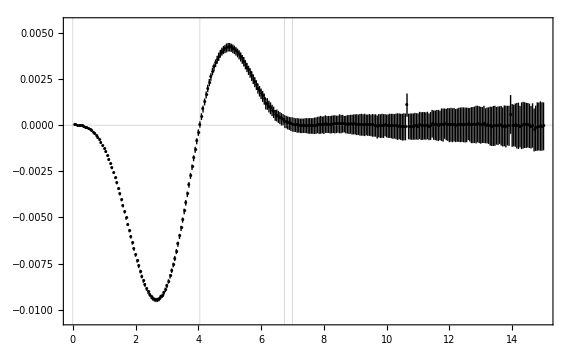

```mathematica
nexttoleadingorderbyshell=ErrorListPlot[Table[{resultsntl[[n,1]],ErrorBar[resultsntl[[n,2]]]},{n,1,Length[resultsntl]}],GridLines->{{0,4.05,6.75,7},{0}},PlotRange->{Automatic,{-0.0105,0.0055}},PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\hat{S}_{\\text{acg}}^{\\circ\\text{ntl}}\\left(k_{\\text{J}}\\beta\\, r\\right)",Magnification->1.25]},RotateLabel->False,ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}]]
```

The following gives the right-hand plot of Figure H1, showing density in space,

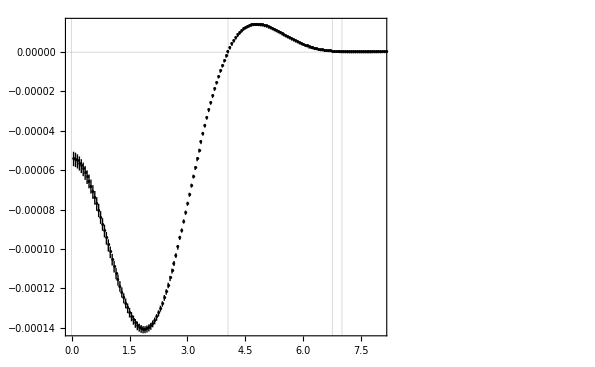

```mathematica
nexttoleadingorderdensity=ErrorListPlot[Table[{{resultsntl[[n,1,1]],resultsntl[[n,1,2]]/(4 π resultsntl[[n,1,1]]^2)},ErrorBar[resultsntl[[n,2]]/(4 π resultsntl[[n,1,1]]^2)]},{n,1,Length[resultsntl]}],GridLines->{{0,4.05,6.75,7},{0}},PlotRange->{{Automatic,8},Full},PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->595,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\frac{\\hat{S}_{\\text{acg}}^{\\circ\\text{ntl}}\\left(k_{\\text{J}}\\beta\\, r\\right)}{4\\pi \\left(k_{\\text{J}}\\beta\\, r\\right)^2}",Magnification->1.25]},RotateLabel->False,
FrameTicks->{{densityframeticks,Automatic},Automatic},ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}]]
```

Now combine the two above plots to create Figure H1 in full,

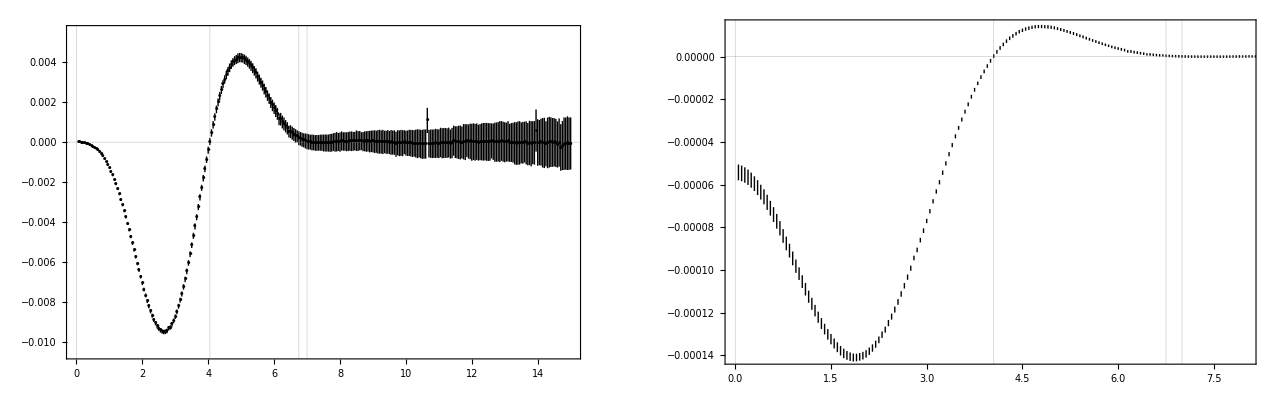

```mathematica
FigureH1=GraphicsRow[{nexttoleadingorderbyshell,nexttoleadingorderdensity},BaselinePosition->Top]
```

If uncommented, the following exports Figure H1,

```mathematica
(* Export["EGCFigureH1.pdf",FigureH1]; *)
```

## Appendix H3: confirming the next-to-leading order distribution over space integrates to the total net entropy creation

Recall the total net entropy creation, calculated above for Appendix H1,

```mathematica
numericalintegration
```

-0.0115541

The next line sums all the values of the next-to-leading order entropy creation pattern function in the calculated range, and multiplies by 0.05000 to get an integrated value of the function, which is very close to the Appendix H1 result,

```mathematica
integratedntl=Sum[resultsntl[[n,1,2]],{n,1,Length[resultsntl]}] 0.05000
```

-0.0115463

The following shows that the minimum size of the entropy creation shell density near r=7 is at r=7.1

```mathematica
Table[{r,ScientificForm[resultsntl[[r  20,1,2]]]},{r,6.5,7.5,0.05}]//MatrixForm
```

(6.5 | 5.23449×10^-4
6.55 | 4.49169×10^-4
6.6 | 3.85598×10^-4
6.65 | 3.1329×10^-4
6.7 | 2.95598×10^-4
6.75 | 1.99136×10^-4
6.8 | 1.67212×10^-4
6.85 | 1.21461×10^-4
6.9 | 9.33093×10^-5
6.95 | 6.06336×10^-5
7. | 3.4889×10^-5
7.05 | 1.65934×10^-5
7.1 | -2.43756×10^-8
7.15 | -1.3913×10^-5
7.2 | -1.84191×10^-5
7.25 | -3.77922×10^-5
7.3 | -3.58015×10^-5
7.35 | -3.40736×10^-5
7.4 | -2.5913×10^-5
7.45 | -2.52294×10^-5
7.5 | -4.30548×10^-5)

The next line sums values of the next-to-leading order entropy creation pattern function out to r=7.1, and again is very close to the Appendix H1 result,

```mathematica
integratedntl7=Sum[resultsntl[[n,1,2]],{n,1,142}]×0.05000
```

-0.011496

## Appendix H4

## Variant of Appendix F approach

This part of the notebook follows that for Appendix F, adapted to the case where the initial perturbation has Maxwellian parameter σ1.

## Variants of quantities that occur in Eq. (F19)

We calculate the additional quantities needed, starting with Y_1(k_+,ⅈ E):

```mathematica
varYpE=Simplify[Normal[Series[-1/(ⅈ ηE)-(σ1^2 (κ kp)^2)/(ⅈ ηE)^3-(3 σ1^4 (κ kp)^4)/(ⅈ ηE)^5-(15 σ1^6 (κ kp)^6)/(ⅈ ηE)^7-(105 σ1^8 (κ kp)^8)/(ⅈ ηE)^9,{κ,0,8}]]];
```

And the function Y_1(k,ω,k_+,ω_+) analogous to Eq. (F17)

```mathematica
varYdouble=Collect[Expand[Expectation[Normal[Series[1/((κ k) vpa-ω) 1/((κ kppa) vpa+(κ kppe) vpe-ωp),{κ,0,8}]],{vpa,vpe}\[Distributed]MultinormalDistribution[{0,0},σ1^2 IdentityMatrix[2]]]],{κ}];
```

We will also need its derivative with respect to ω:

```mathematica
vardYdouble=D[varYdouble,ω];
```

Write Y_1(k_1,ⅈ η_1,k_+,ⅈ E) and Y_1(k_2,ⅈ η_2,k_+,ⅈ E), and also related derivatives:

```mathematica
varY11pE=Simplify[(varYdouble//.{k->k1,kppa->k1dotkp/k1,kppe->√(kp^2-kppa^2)})/.{ω->ⅈ η1,ωp->ⅈ ηE}];
```

```mathematica
varY22pE=Simplify[(varYdouble//.{k->k2,kppa->k2dotkp/k2,kppe->√(kp^2-kppa^2)})/.{ω->ⅈ η2,ωp->ⅈ ηE}];
```

```mathematica
vardY11pE=Simplify[(vardYdouble//.{k->k1,kppa->k1dotkp/k1,kppe->√(kp^2-kppa^2)})/.{ω->ⅈ η1,ωp->ⅈ ηE}];
```

```mathematica
vardY22pE=Simplify[(vardYdouble//.{k->k2,kppa->k2dotkp/k2,kppe->√(kp^2-kppa^2)})/.{ω->ⅈ η2,ωp->ⅈ ηE}];
```

## Variant evaluation of Eqs. (F19) and (F20) to get Eq. (F22)

This then enables us to write a series expansion for the variant of Eq. (F19) as

```mathematica
varID1=Normal[Series[(((Subscript[k, J]^2 P11)/(κ k1)^2 (varY22pE+(Subscript[k, J]^2 P22pE varYpE)/((κ kp)^2-Subscript[k, J]^2 PpE))+(Subscript[k, J]^2 κ^2 k1dotkp P11 Y22 varYpE)/((κ k1)^2 ((κ kp)^2-Subscript[k, J]^2 PpE)) V q2+(Subscript[k, J]^2 σ^2 κ^2 k1dotk2 Y22)/(κ k2)^2 (vardY11pE+(Subscript[k, J]^2 varYpE)/((κ kp)^2-Subscript[k, J]^2 PpE) dP11pE) (V q2+1))+((Subscript[k, J]^2 P22)/(κ k2)^2 (varY11pE+(Subscript[k, J]^2 P11pE varYpE)/((κ kp)^2-Subscript[k, J]^2 PpE))+(Subscript[k, J]^2 κ^2 k2dotkp P22 Y11 varYpE)/((κ k2)^2 ((κ kp)^2-Subscript[k, J]^2 PpE)) V q1+(Subscript[k, J]^2 σ^2 κ^2 k1dotk2 Y11)/(κ k1)^2 (vardY22pE+(Subscript[k, J]^2 varYpE)/((κ kp)^2-Subscript[k, J]^2 PpE) dP22pE) (V q1+1))),{κ,0,8}]];
```

We can then derive the variant of Eq. (F22):

```mathematica
varF22expression=Collect[Series[F20remaining varID1,{κ,0,2}]//.{k2dotkp->kp^2-k1dotkp,k1dotk2->k1dotkp-k1^2,k2^2->kp^2+k1^2-2 k1dotkp},{κ,k1dotv1 },Simplify]
```

k1dotv1^2/(4 k1^2 σ^2)+κ^2 (-k1dotv1^4/(4 k1^2 σ^4 k_J^2)+(k1dotv1^2 (4 k1dotkp^2 σ^2+k1^2 kp^2 (23 σ^2-3 σ1^2)+3 kp^4 (3 σ^2-σ1^2)+3 k1dotkp kp^2 (-6 σ^2+σ1^2)))/(12 k1^2 kp^2 σ^4 k_J^2))+κ (-(ⅈ k1dotv1^3)/(4 k1^2 σ^3 k_J)+(ⅈ k1dotv1 (8 k1dotkp^2 σ^2+k1^2 kp^2 (37 σ^2-6 σ1^2)+6 kp^4 (3 σ^2-σ1^2)+6 k1dotkp kp^2 (-6 σ^2+σ1^2)))/(24 k1^2 kp^2 σ^3 k_J))+(ⅈ k1dotv1 k_J)/(4 k1^2 κ σ)

The following confirms that our varF22expression is the same as F22expression, when σ1 is set to σ,

```mathematica
Simplify[((varF22expression)/.{σ1->σ})-F22expression]
```

0

Set the dummy variable κ to 1 in varF22expression to get the final expression:

```mathematica
varF22expressionNoκ=varF22expression/.{κ->1}
```

k1dotv1^2/(4 k1^2 σ^2)-k1dotv1^4/(4 k1^2 σ^4 k_J^2)+(k1dotv1^2 (4 k1dotkp^2 σ^2+k1^2 kp^2 (23 σ^2-3 σ1^2)+3 kp^4 (3 σ^2-σ1^2)+3 k1dotkp kp^2 (-6 σ^2+σ1^2)))/(12 k1^2 kp^2 σ^4 k_J^2)-(ⅈ k1dotv1^3)/(4 k1^2 σ^3 k_J)+(ⅈ k1dotv1 (8 k1dotkp^2 σ^2+k1^2 kp^2 (37 σ^2-6 σ1^2)+6 kp^4 (3 σ^2-σ1^2)+6 k1dotkp kp^2 (-6 σ^2+σ1^2)))/(24 k1^2 kp^2 σ^3 k_J)+(ⅈ k1dotv1 k_J)/(4 k1^2 σ)

The above expression is the factor on the right-hand side of the variant of Eq. (F22), in braces, which when multiplied by the Maxwellian and the time exponential, as set out in that equation, gives the variant γ_a(k_1,v_1,k_2,t).

## Variant of Appendix G approach

This part of the notebook follows that for Appendix G, adapted to the case where the initial perturbation has Maxwellian parameter σ1.

## Calculating the variant driving matrix (D̃)_1

From Eq. (F3), neglecting terms of higher order in V^-1, and leaving aside Maxwellian factors, we have

```mathematica
D1tilde0[k1_,v1_,k2_,v2_,kp_]:=(ⅈ Subscript[k, J]^2 kp.v1)/(kp.kp) intf10[kp] V q[k2]+(ⅈ Subscript[k, J]^2)/(k2.k2) σ^2 k2.df10[kp,v1] (V q[k2]+1)+(ⅈ Subscript[k, J]^2 k1.v1)/(k1.k1) f10[kp,v2]+(ⅈ Subscript[k, J]^2 kp.v2)/(kp.kp) intf10[kp] V q[k1]+(ⅈ Subscript[k, J]^2)/(k1.k1) σ^2 k1.df10[kp,v2] (V q[k1]+1)+(ⅈ Subscript[k, J]^2 k2.v2)/(k2.k2) f10[kp,v1]
```

```mathematica
D1tilde11[k1_,v1_,k2_,v2_,kp_]:=(ⅈ Subscript[k, J]^2)/(k2.k2) σ^2 k2.df11[kp,v1] (V q[k2]+1)+(ⅈ Subscript[k, J]^2 k2.v2)/(k2.k2) f11[kp,v1]
```

```mathematica
D1tilde12[k1_,v1_,k2_,v2_,kp_]:=(ⅈ Subscript[k, J]^2 k1.v1)/(k1.k1) f11[kp,v2]+(ⅈ Subscript[k, J]^2)/(k1.k1) σ^2 k1.df11[kp,v2] (V q[k1]+1)
```

where D1tilde0 is associated with Maxwellians with parameter σ, while D1tilde11 and D1tilde12 are associated with a Maxwellian with parameter σ1, in respectively v1 or v2.   We now adapt the approach used above in calculating the driving matrix for Appendix G.

We start by defining another series approximations using the function Zapprox from above,

```mathematica
Y1approx[p_,ω_,κ_,numberofYterms_]:=1/(κ √(2 p.p) σ1) Zapprox[ω/(κ √(2 p.p) σ1),numberofYterms]
```

From Eq. (H10), we have, leaving aside the Maxwellian factor, a series expansion for f10 as

```mathematica
FullSimplify[((Normal[Series[-(ⅈ Subscript[k, J]^2 κ p.v Y1approx[p,ω,κ,4])/((κ p.v-ω)(κ^2 p.p-Subscript[k, J]^2 Papprox2[p,ω,κ,3])),{κ,0,4}]])/.κ->1)]
```

-1/(ω^5 p.p (ω^2+σ^2 k_J^2)^3)ⅈ p.v (ω+p.v) k_J^2 ((ω^4+ω^2 (p.v)^2+(p.v)^4) (ω^2+σ^2 k_J^2)^2+p.p (ω^2+(p.v)^2) (ω^2+σ^2 k_J^2) (σ1^2 ω^2+σ^2 (-3 σ^2+σ1^2) k_J^2)+3 (p.p)^2 (σ1^4 ω^4-σ^2 (5 σ^4+σ^2 σ1^2-2 σ1^4) ω^2 k_J^2+σ^4 (-2 σ^4-σ^2 σ1^2+σ1^4) k_J^4))

```mathematica
f10[p_,v_]:=-1/(ω^5 p.p (ω^2+σ^2 Subscript[k, J]^2)^3)ⅈ p.v (ω+p.v) Subscript[k, J]^2 ((ω^4+ω^2 (p.v)^2+(p.v)^4) (ω^2+σ^2 Subscript[k, J]^2)^2+p.p (ω^2+(p.v)^2) (ω^2+σ^2 Subscript[k, J]^2) (σ1^2 ω^2+σ^2 (-3 σ^2+σ1^2) Subscript[k, J]^2)+3 (p.p)^2 (σ1^4 ω^4-σ^2 (5 σ^4+σ^2 σ1^2-2 σ1^4) ω^2 Subscript[k, J]^2+σ^4 (-2 σ^4-σ^2 σ1^2+σ1^4) Subscript[k, J]^4))
```

and for f11,

```mathematica
FullSimplify[((Normal[Series[-ⅈ/(κ p.v-ω),{κ,0,4}]])/.κ->1)]
```

(ⅈ (ω^4+p.v (ω+p.v) (ω^2+(p.v)^2)))/ω^5

```mathematica
f11[p_,v_]:=(ⅈ (ω^4+p.v (ω+p.v) (ω^2+(p.v)^2)))/ω^5
```

Now for intf10,

```mathematica
FullSimplify[((Normal[Series[-ⅈ Y1approx[p,ω,κ,4]-(ⅈ Subscript[k, J]^2 Papprox2[p,ω,κ,3] Y1approx[p,ω,κ,4])/(κ^2 p.p-Subscript[k, J]^2 Papprox2[p,ω,κ,3]),{κ,0,4}]])/.κ->1)]
```

1/((ω^3+σ^2 ω k_J^2)^3)ⅈ (ω^4 (ω^2+σ^2 k_J^2)^2+ω^2 p.p (ω^2+σ^2 k_J^2) (σ1^2 ω^2+σ^2 (-3 σ^2+σ1^2) k_J^2)+3 (p.p)^2 (σ1^4 ω^4-σ^2 (5 σ^4+σ^2 σ1^2-2 σ1^4) ω^2 k_J^2+σ^4 (-2 σ^4-σ^2 σ1^2+σ1^4) k_J^4))

```mathematica
intf10[p_]:=1/((ω^3+σ^2 ω Subscript[k, J]^2)^3)ⅈ (ω^4 (ω^2+σ^2 Subscript[k, J]^2)^2+ω^2 p.p (ω^2+σ^2 Subscript[k, J]^2) (σ1^2 ω^2+σ^2 (-3 σ^2+σ1^2) Subscript[k, J]^2)+3 (p.p)^2 (σ1^4 ω^4-σ^2 (5 σ^4+σ^2 σ1^2-2 σ1^4) ω^2 Subscript[k, J]^2+σ^4 (-2 σ^4-σ^2 σ1^2+σ1^4) Subscript[k, J]^4))
```

For df10:

```mathematica
Simplify[((Normal[Series[-(ⅈ Subscript[k, J]^2 Y1approx[p,ω,κ,4])/((κ p.v-ω)(κ^2 p.p-Subscript[k, J]^2 Papprox2[p,ω,κ,3]))(κ p-(κ p.v v)/σ^2-(κ^2 p.v p)/(κ p.v-ω)),{κ,0,4}]])/.κ->1)]
```

1/(σ^2 ω^5 p.p (ω^2+σ^2 k_J^2)^3)ⅈ k_J^2 (-(p σ^2 ω^5+ω^4 (2 p σ^2-v ω) p.v+ω^3 (3 p σ^2-v ω) (p.v)^2+ω^2 (4 p σ^2-v ω) (p.v)^3+ω (5 p σ^2-v ω) (p.v)^4+(6 p σ^2-v ω) (p.v)^5-v (p.v)^6) (ω^2+σ^2 k_J^2)^2+p.p (p σ^2 ω^3+ω^2 (2 p σ^2-v ω) p.v+ω (3 p σ^2-v ω) (p.v)^2+(4 p σ^2-v ω) (p.v)^3-v (p.v)^4) (ω^2+σ^2 k_J^2) (-σ1^2 ω^2+(3 σ^4-σ^2 σ1^2) k_J^2)+3 (p.p)^2 (p σ^2 ω+(2 p σ^2-v ω) p.v-v (p.v)^2) (-σ1^4 ω^4+σ^2 (5 σ^4+σ^2 σ1^2-2 σ1^4) ω^2 k_J^2+(2 σ^8+σ^6 σ1^2-σ^4 σ1^4) k_J^4))

```mathematica
df10[p_,v_]:=1/(σ^2 ω^5 p.p (ω^2+σ^2 Subscript[k, J]^2)^3)ⅈ Subscript[k, J]^2 (-(p σ^2 ω^5+ω^4 (2 p σ^2-v ω) p.v+ω^3 (3 p σ^2-v ω) (p.v)^2+ω^2 (4 p σ^2-v ω) (p.v)^3+ω (5 p σ^2-v ω) (p.v)^4+(6 p σ^2-v ω) (p.v)^5-v (p.v)^6) (ω^2+σ^2 Subscript[k, J]^2)^2+p.p (p σ^2 ω^3+ω^2 (2 p σ^2-v ω) p.v+ω (3 p σ^2-v ω) (p.v)^2+(4 p σ^2-v ω) (p.v)^3-v (p.v)^4) (ω^2+σ^2 Subscript[k, J]^2) (-σ1^2 ω^2+(3 σ^4-σ^2 σ1^2) Subscript[k, J]^2)+3 (p.p)^2 (p σ^2 ω+(2 p σ^2-v ω) p.v-v (p.v)^2) (-σ1^4 ω^4+σ^2 (5 σ^4+σ^2 σ1^2-2 σ1^4) ω^2 Subscript[k, J]^2+(2 σ^8+σ^6 σ1^2-σ^4 σ1^4) Subscript[k, J]^4))
```

And for df11:

```mathematica
Simplify[((Normal[Series[(ⅈ κ p)/(κ p.v-ω)^2+(ⅈ v/σ1^2)/(κ p.v-ω),{κ,0,4}]])/.κ->1)]
```

(ⅈ (ω^3 (p σ1^2-v ω)+ω^2 (2 p σ1^2-v ω) p.v+ω (3 p σ1^2-v ω) (p.v)^2+(4 p σ1^2-v ω) (p.v)^3-v (p.v)^4))/(σ1^2 ω^5)

```mathematica
df11[p_,v_]:=1/(σ1^2 ω^5)ⅈ (ω^3 (p σ1^2-v ω)+ω^2 (2 p σ1^2-v ω) p.v+ω (3 p σ1^2-v ω) (p.v)^2+(4 p σ1^2-v ω) (p.v)^3-v (p.v)^4)
```

## Calculating the variant of the vector ν (nu)

Eq. (G10) defines  the vector ν. Its first component is μ^(0) which is 0.  The second, fourth and sixth components are given by ν^(j)(k_1,k_2) for j=1,2,3.  The third, fifth and seventh are similarly ν^(j)(k_2,k_1).We write k_1 and k_2 in co-ordinate terms with their moduli k1 and k2, and the angle θ, which  k_2 makes to k_1; and we also now introduce the dummy variable κ.  Calculating the variant of ν allowing σ1≠σ takes less than two minutes on a standard PC:

```mathematica
varν=Join[{0},Flatten[Table[{term=(Normal[Series[Expectation[ⅈ(κ k1 v1x)^j D1tilde0[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0},{κ k1+κ k2 Cos[θ],κ k2 Sin[θ],0}] G4factor[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0}],{v1x,v1y,v2x,v2y}\[Distributed]MultinormalDistribution[{0,0,0,0},σ^2 IdentityMatrix[4]]],{κ,0,3}]]+Normal[Series[Expectation[ⅈ(κ k1 v1x)^j D1tilde11[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0},{κ k1+κ k2 Cos[θ],κ k2 Sin[θ],0}] G4factor[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0}],{v1x,v1y,v2x,v2y}\[Distributed]MultinormalDistribution[{0,0,0,0},DiagonalMatrix[{σ1^2,σ1^2,σ^2,σ^2}]]],{κ,0,3}]]+Normal[Series[Expectation[ⅈ(κ k1 v1x)^j D1tilde12[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0},{κ k1+κ k2 Cos[θ],κ k2 Sin[θ],0}] G4factor[{κ k1,0,0},{v1x,v1y,0},{κ k2 Cos[θ],κ k2 Sin[θ],0},{v2x,v2y,0}],{v1x,v1y,v2x,v2y}\[Distributed]MultinormalDistribution[{0,0,0,0},DiagonalMatrix[{σ^2,σ^2,σ1^2,σ1^2}]]],{κ,0,3}]]),term/.{k1->k2,k2->k1,θ->-θ}},{j,1,3}]]];
```

## Calculating the variant result, γ_a

The matrices M, L^-1 and Γ, and quantity smallγcoefficient have already been calculated above - they are independent of σ1 - so we can now write the variant (γ̃)_a, to second order in κ, as

```mathematica
varγtilde=Series[smallγcoefficient Γcoefficients.LInverse.varν,{κ,0,2}];
```

To wrap up, we need to take the residue of this at (approximately) ω=ⅈη_1+ⅈη_2, which was calculated as ωres above, and we applying the residue theorem in the next line, keeping the result up to and including second order in κ.  This takes five to ten minutes on a standard PC.

```mathematica
varγ=Series[Limit[-ⅈ*Simplify[varγtilde(ω-ωres)],ω->ωres],{κ,0,2}];
```

We can put this into a more convenient form using the displayrule from above, which then gives us the final result for the variant of Eq. (G11) needed for Appendix H4, leaving aside the Maxwellian and exponential terms,

```mathematica
varGgammaexpression=Collect[varγ//.displayrule,κ,Simplify]
```

k1dotv1^2/(4 k1^2 σ^2)+(k1dotv1^2 κ^2 (-3 k1dotv1^2 kp^2+4 k1dotkp^2 σ^2+k1^2 kp^2 (23 σ^2-3 σ1^2)+3 kp^4 (3 σ^2-σ1^2)+3 k1dotkp kp^2 (-6 σ^2+σ1^2)))/(12 k1^2 kp^2 σ^4 k_J^2)+(ⅈ k1dotv1 κ (-6 k1dotv1^2 kp^2+8 k1dotkp^2 σ^2+k1^2 kp^2 (37 σ^2-6 σ1^2)+6 kp^4 (3 σ^2-σ1^2)+6 k1dotkp kp^2 (-6 σ^2+σ1^2)))/(24 k1^2 kp^2 σ^3 k_J)+(ⅈ k1dotv1 k_J)/(4 k1^2 κ σ)

The following confirms that our varGgammaexpression is the same as varF22expression calculated above,

```mathematica
Simplify[varGgammaexpression-varF22expression]
```

0

## Preparing and doing the variant numerical integration

We now, as in Eq. (H1), need to swap k_1↔-k_+ in the above expression,

```mathematica
varH1expression=varF22expression/.{k1dotv1->-kpdotv1,k1->-kp,kp->-k1};
```

We can also find the variant of the derivative-related expression in Eq. (H2), writing k1vect to represent the vector quantity k_1, which, as for its scalar cousins, attracts a factor of κ,

```mathematica
η=Subscript[k, J] σ-(3 σ (κ k1)^2)/(2 Subscript[k, J])+(15 σ (κ k1)^4)/(8 Subscript[k, J]^3);
```

```mathematica
Y1=-(1/(ⅈ η)+(σ1^2 (κ k1)^2)/(ⅈ η)^3 +(3 σ1^4 (κ k1)^4)/(ⅈ η)^5+(15 σ1^6 (κ k1)^6)/(ⅈ η)^7);
```

```mathematica
varH2expression=Collect[Normal[Series[-(ⅈ Subscript[k, J]^2 σ^2 κ k1vect V η Y1)/((κ k1dotv1-ⅈ η)(σ^2(Subscript[k, J]^2-(κ k1)^2)-η^2))(1-(κ k1dotv1)/(κ k1dotv1-ⅈ η)),{κ,0,2}]],κ,Simplify];
```

To get the variant integrand of Eq. (29) (still leaving aside the exponential factors, which we assume to be constant over the integration), we need to multiply varH1expression with the dot product of k_2/(κ k_2^2)and varH2expression,

```mathematica
varEq29integrand=varH1expression varH2expression/k1vect k1dotk2/(κ k2^2);
```

In the next two lines, we now integrate this with respect to v_1, to get the variant of the result set out in Eq. (H3).  To do this, we again define vx to be the component of v_1 parallel to k_1, and vy to be the other component of v_1 which lies in the plane made by k_1 and k_2 (or an arbitrary direction perpendicular to k_1, if k_1 and k_2 are co-linear).  We also write cth for the cosine of the angle θ between k_1 and k_2. Then we can write

```mathematica
varEq29integranda=Simplify[varEq29integrand/.{k1dotv1->k1 vx,kpdotv1->k1 vx+k2(cth vx + √(1-cth^2) vy)}];
```

where the term within round brackets is k2dotv1.  We now do the v_1 integration, using Gaussian moments, via the appropriate Mathematica function, to get

```mathematica
varH3expression=Collect[Series[Expectation[varEq29integranda,{vx,vy}\[Distributed]MultinormalDistribution[{0,0},σ^2 IdentityMatrix[2]]],{κ,0,0}],{V,κ},Simplify];
```

The corresponding expression from the notebook for Appendix G1-3, with σ1=σ, is

```mathematica
H3expression
```

V (-1/(48 k1^4 k2^2 kp^2 σ k_J)ⅈ k1dotk2 (15 k1^6+18 cth k1^5 k2-8 k1dotkp^2 k2^2+18 cth k1^3 k2 (2 k2^2-kp^2)+k1^4 (-30 k1dotkp+3 (-5+12 cth^2) k2^2+22 kp^2)+2 k1^2 (4 k1dotkp^2+15 k1dotkp k2^2+9 k2^4-20 k2^2 kp^2))-(ⅈ k1dotk2 (k1^2-k2^2) k_J)/(8 k1^2 k2^2 kp^2 κ^2 σ))

The following confirms that the new expression, with σ1 set to σ is the same as the old expression,

```mathematica
Simplify[Collect[varH3expression/.σ1->σ,κ,Simplify]-H3expression]
```

0

Our varH3expression can be split into an order -2 expression

```mathematica
varH3expressionorderm2=Collect[SeriesCoefficient[varH3expression,{κ,0,-2}],{V,κ},Simplify]
```

-(ⅈ k1dotk2 (k1^2-k2^2) V k_J)/(8 k1^2 k2^2 kp^2 σ)

That is the same as for the main, non-variant, model with σ1=σ,

```mathematica
Simplify[varH3expressionorderm2-H3expressionorderm2]
```

0

We also have an order 0 expression,

```mathematica
varH3expressionorder0=Collect[SeriesCoefficient[varH3expression,{κ,0,0}],{V,κ},Simplify]
```

-1/(48 k1^4 k2^2 kp^2 σ^3 k_J)ⅈ k1dotk2 V (18 cth k1^5 k2 σ^2-8 k1dotkp^2 k2^2 σ^2+18 cth k1^3 k2 (2 k2^2-kp^2) σ^2+3 k1^6 (9 σ^2-4 σ1^2)+2 k1^2 (4 k1dotkp^2 σ^2+9 k2^4 σ^2+3 k1dotkp k2^2 (6 σ^2-σ1^2)+k2^2 kp^2 (-23 σ^2+3 σ1^2))+k1^4 (2 kp^2 (14 σ^2-3 σ1^2)+6 k1dotkp (-6 σ^2+σ1^2)+3 k2^2 (3 (-3+4 cth^2) σ^2+4 σ1^2)))

This is as far as we can go analytically, so we now take out the constants V and k_J from the expression, put k_+ in terms of k_1, k_2 and cth, and then integrate numerically.  To prepare for this, we multiply by σ^3 as opposed to σ in the notebook for Appendix F1-3,

```mathematica
varH3expressionorder0fornumerical=Simplify[(varH3expressionorder0 /.{kp->√(k1^2+k2^2+2 k1 k2 cth),k1dotk2->k1 k2 cth,k1dotkp->k1^2+k1 k2 cth})(σ^3 Subscript[k, J])/V]
```

-1/(48 k1 k2 (k1^2+2 cth k1 k2+k2^2))ⅈ cth (3 k1^4 (9 σ^2-4 σ1^2)-2 k2^4 (2 (7+2 cth^2) σ^2-3 σ1^2)+6 cth k1^3 k2 (6 σ^2-σ1^2)+6 cth k1 k2^3 (-9 σ^2+σ1^2)+k1^2 k2^2 ((-17+8 cth^2) σ^2+6 σ1^2))

From the above, we can see that the expression contains various combinations of σ1 and σ.  We therefore form a CoefficientList before doing the numerical integration,

```mathematica
varH3expressionorder0fornumericallist=CoefficientList[varH3expressionorder0fornumerical,{σ,σ1}];
```

We now doing the numerical integrations, keeping track of estimated errors, and dividing by σ^2 to maintain compatibility with the result of the notebook for Appendix G1-3,

```mathematica
varerrors=ConstantArray[Null,{3,3}];varnumericalintegration=Expand[1/σ^2 Chop[Sum[σ^n σ1^n1 (-ⅈ NIntegrate[Boole[(k1^2+k2^2+2 k1 k2 cth)≤1] (k1^2 k2^2 varH3expressionorder0fornumericallist[[n+1,n1+1]]),{cth,-1,1},{k1,0,1},{k2,0,1},AccuracyGoal->5,IntegrationMonitor:>((varerrors[[n+1,n1+1]]=Through[#1@"Error"])&)]),{n,0,2},{n1,0,2}]]]
```

-0.00830719-(0.00324639 σ1^2)/σ^2

which can also be written as

```mathematica
ScientificForm[varnumericalintegration,3]
```

-8.31×10^-3-((3.25×10^-3) σ1^2)/σ^2

We check that, in the σ1=σ case, this gives essentially the same answer as in the Appendix G1-3 notebook

```mathematica
paddedscientificform[((((varnumericalintegration)/.{σ1->σ})-numericalintegration)/numericalintegration) 100,1]
```

-5.×10^-3

which it does to within around 0.005%.

The estimated errors of our numerical integrations are, in the order of ascending powers of σ1,

```mathematica
varerrorlist={Total[varerrors[[2+1,0+1]]],Total[varerrors[[0+1,2+1]]]}
```

{9.73605×10^-6,9.99946×10^-6}

which can be written as

```mathematica
ScientificForm[varerrorlist,1]
```

{1.×10^-5,1.×10^-5}

## Calculating next-to-leading order distribution over space plots for the limit σ1→0, and plotting Figure H2

This part of the notebook is along the lines of the similar part of the Appendix H1-3.

For calculating the distribution over space, we need to modify varH2expression from above, changing occurrences of k_1 to k_01,

```mathematica
varH2expression01=varH2expression/.{k1->k01,k1dotv1->k01dotv1,k1vect->k01vect};
```

Then putting varH2expression01 in the form

```mathematica
varH2expression01a=varH2expression01/.{k01->√(k01v.k01v),k01dotv1->k01v.v1v};
```

Now for varH1expression, found above, the corresponding form is

```mathematica
varH1expressiona=Simplify[varH1expression/.{kpdotv1->k12v.v1v,kp->√(k12v.k12v),k1->√(k1v.k1v),k1dotkp->k1v.k12v}];
```

Now combine H1expressiona and H2expression01a to get the required integrand to be the variant and next-to-leading order version of Eq. (H7), other than the sinc-related function and the (2π)^-3 factors, and pick out the terms of order 0 in κ,

```mathematica
varintegrandexpression=Simplify[SeriesCoefficient[((varH1expressiona varH2expression01a/k01vect (k01v.k2v)/(κ k2v.k2v))/.σ1->0),{κ,0,0}]];
```

We now do the integration with respect to v_1, using Gaussian moments, via the appropriate Mathematica function, and extract non-numerical constants,

```mathematica
varintegratedoverv1expression=Simplify[ (σ Subscript[k, J])/V Expectation[varintegrandexpression,v1v\[Distributed]MultinormalDistribution[{0,0,0},σ^2 IdentityMatrix[3]]]];
```

The following function then does the required numerical integration, for next-to-leading order,

```mathematica
integraterntl[r_]:=Module[{int,errors},int=Chop[Quiet[NIntegrate[-ⅈ/(2 π^2) Boole[(k1^2+k2^2+2 k1 k2 cth≤1)&&(k1^2+k0^2+2 k1 k0 cpsi≤1)] k0 k1^2 k2^2 r Sin[r k0] varintegratedoverv1expression,{k1,0,2},{k2,0,1},{k0,0,3},{ϕ,0,2 π},{cth,-1,1},{cpsi,-1,1},PrecisionGoal->5,IntegrationMonitor:>((errors=Through[#1@"Error"])&)]]];
{{r,int},Total@errors,(Total@errors)/Abs[int]}]
```

returning - as for its leading order equivalent, integrater - a pair of the r (radius) value input and the result, an error estimate, and a relative error estimate.  Again, as for its the corresponding leading order function, integrater, without Quiet, this function will typically give rise to (non-fatal) error messages, so keeping track of error estimates is important.

The quick approach is to import the results of integration for the radii r=0.05000, 0.10000,0.15000...15.00000 from the data file,

```mathematica
varresultsntl=<<"Data for Entropy and gravitational collapse Wren 2018.m"[[4]];
```

Alternatively, the results can be calculated (and exported) using the following code, when uncommented.  This takes about four to six hours on a standard PC:

```mathematica
(*( varresultsntl={};Monitor[For[r=0.05000,r≤15,r=r+0.05000,varresultsntl=Join[varresultsntl,{integraterntl[r]}]]
,varresultsntl//MatrixForm//ScientificForm];Export["Appendix G4 Variant data.m",varresultsntl];varresultsntl//MatrixForm//ScientificForm )*)
```

The following gives the left-hand plot of Figure H2, showing the stationary entropy-creation pattern function by shell,

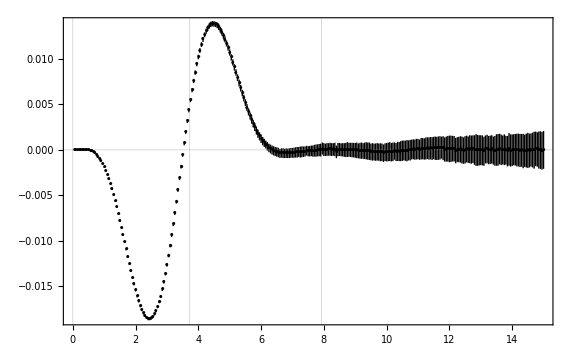

```mathematica
statnexttoleadingorderbyshell=ErrorListPlot[Table[{varresultsntl[[n,1]],ErrorBar[varresultsntl[[n,2]]]},{n,1,Length[varresultsntl]}],GridLines->{{0,3.725,7.925},{0}},PlotRange->Full,PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->Large,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\hat{S}_{\\text{acg}}^{\\circ\\text{\\,stat\\,ntl}}\\left(k_{\\text{J}}\\beta\\, r\\right)",Magnification->1.25]},RotateLabel->False,ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}]]
```

And now the right-hand plot of Figure H2, showing the stationary entropy-creation pattern function by volume,

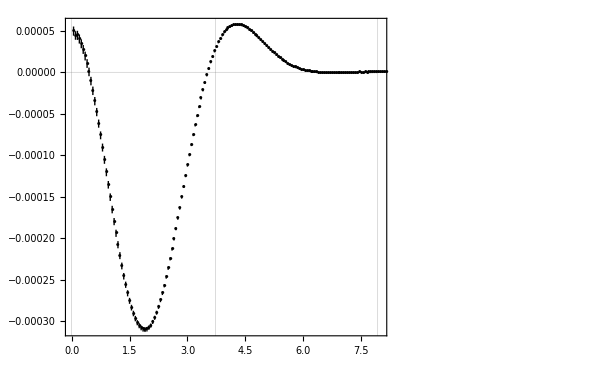

```mathematica
statnexttoleadingorderdensity=ErrorListPlot[Table[{{varresultsntl[[n,1,1]],varresultsntl[[n,1,2]]/(4 π varresultsntl[[n,1,1]]^2)},ErrorBar[varresultsntl[[n,2]]/(4 π varresultsntl[[n,1,1]]^2)]},{n,1,Length[varresultsntl]}],GridLines->{{0,3.725,7.925},{0}},PlotRange->{{Automatic,8},Full},PlotStyle->{Thin,Black},PlotMarkers->{Automatic,2},ImageSize->595,FrameStyle->BlackFrame,FrameLabel->{MaTeX["k_{\\text{J}}\\beta\\, r",Magnification->1.25],MaTeX["\\frac{\\hat{S}_{\\text{acg}}^{\\circ\\text{\\,stat\\,ntl}}\\left(k_{\\text{J}}\\beta\\, r\\right)}{4\\pi \\left(k_{\\text{J}}\\beta\\, r\\right)^2}",Magnification->1.25]},RotateLabel->False,
FrameTicks->{{vardensityframeticks,vardensityframeticksright},Automatic},ErrorBarFunction->Function[{coords, errs}, {Opacity[1],Line[{{coords[[1]],coords[[2]]-errs⟦2,1⟧},{coords[[1]],coords[[2]]+errs⟦2,1⟧}}]}]]
```

Now combine the two above plots to create Figure H2 in full,

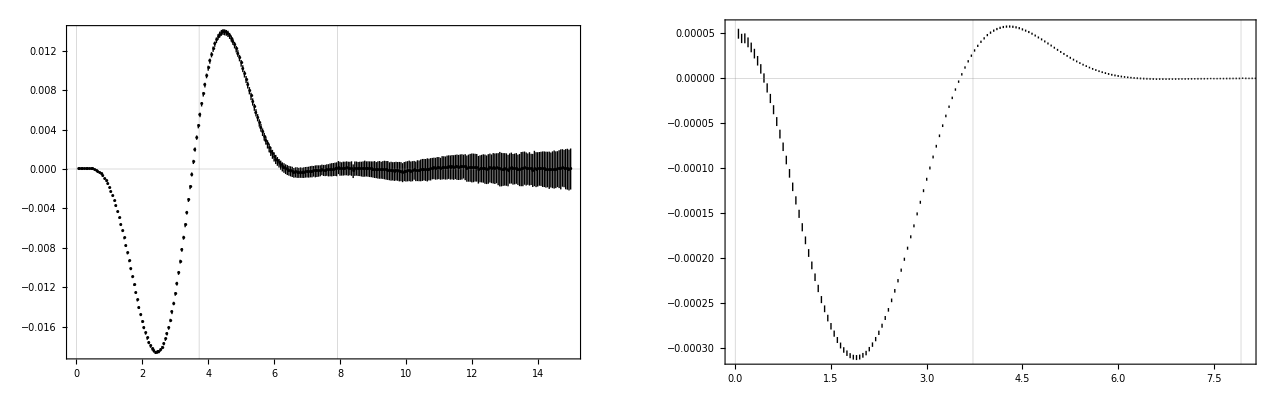

```mathematica
FigureH2=GraphicsRow[{statnexttoleadingorderbyshell,statnexttoleadingorderdensity},BaselinePosition->Top]
```

If uncommented, the following exports Figure H2,

```mathematica
(*Export["EGCFigureH2.pdf",FigureH2]; *)
```

If uncommented, and if the relevant datasets have been calculated above, the following produces the data file “Data for Entropy and gravitational collapse Wren 2018 data.m”.

```mathematica
(*Export["Data for Entropy and gravitational collapse Wren 2018.m",{B3data,results,resultsntl,varresultsntl}]*)
```

## Creating the data file

If uncommented, and if the relevant datasets have been calculated above, the following produces the data file “Data for Entropy and gravitational collapse Wren 2018 data.m”.

```mathematica
(*Export["Data for Entropy and gravitational collapse Wren 2018.m",{B3data,results,resultsntl,varresultsntl}]*)
```

#### End of main notebook

## The remainder of the notebook contains initialisation cells that are automatically evaluated first. They are used for formatting Figures, and for scientific form numbers

For formatting Figures

Define theme and colours:

```mathematica
$PlotTheme="Scientific";
```

```mathematica
colors=(("DefaultPlotStyle"/.(Method/.Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/.Directive[x_,__]:>x)
```

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

Define the formats for the plot lines:

```mathematica
ps8log={{colors[[1]],Dotted},{colors[[2]],Dashing[{0.005,0.005}]},{colors[[3]],Dashing[{0.01,0.01}]},{colors[[4]],Dashing[{0.02,0.02}]}};
```

```mathematica
ps8=Join[{Black},ps8log];
```

Set up the MaTeX package

```mathematica
Needs["MaTeX`"]
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xfrac}","\\usepackage[T1]{fontenc}"}];
```

```mathematica
texStyle={FontFamily->"Latin Modern Roman",FontSize->12};DefaultBaseStyle->texStyle;
```

Define the frame ticks for Figure B1 (Right):

```mathematica
laxsticks={{{{1-1*10^-2,MaTeX["-10^{-2}+1"]},{1-1*10^-3,MaTeX["-10^{-3}+1"]},{1+1*10^-3,MaTeX["10^{-3}+1"]},{1+1*10^-2,MaTeX["10^{-2}+1"]}},None},{Automatic,None}};
```

Define the legend for Figure B1:

```mathematica
magn=1.5;pl={MaTeX["\\text{Numerical solution}",Magnification->magn],MaTeX["k_\\text{J}\\sigma-\\frac{3\\sigma k^2}{2 k_\\text{J}}",Magnification->magn],MaTeX["k_\\text{J}\\sigma-\\cdots+\\frac{15\\sigma k^4}{8 k_\\text{J}^3}",Magnification->magn],MaTeX["k_\\text{J}\\sigma-\\cdots-\\frac{147\\sigma k^6}{16 k_\\text{J}^5}",Magnification->magn],MaTeX["k_\\text{J}\\sigma-\\cdots+\\frac{9531\\sigma k^8}{128 k_\\text{J}^7}",Magnification->magn]};
```

The following defines frame ticks for the right-hand plots of Figures 2 and H1:

```mathematica
densityframeticks={{-1/10000,"-10 ×\!\(\*SuperscriptBox[\(10\), \(-5\)]\)"},{-1/20000,"-5 ×\!\(\*SuperscriptBox[\(10\), \(-5\)]\)"},{-3/10000,"-15 ×\!\(\*SuperscriptBox[\(10\), \(-5\)]\)"},{3/100000,"",{0.005,0}},{1/50000,"",{0.005,0}},{1/100000,"",{0.005,0}},{0,"",{0.005,0}},{-1/100000,"",{0.005,0}},{-1/50000,"",{0.005,0}},{0,"0"},{-3/100000,"",{0.005,0}},{-1/25000,"",{0.005,0}},{-1/20000,"",{0.005,0}},{-3/50000,"",{0.005,0}},{-7/100000,"",{0.005,0}},{-1/12500,"",{0.005,0}},{-9/100000,"",{0.005,0}},{-1/10000,"",{0.005,0}},{-11/100000,"",{0.005,0}},{-3/25000,"",{0.005,0}},{-13/100000,"",{0.005,0}},{-7/50000,"",{0.005,0}},{-3/20000,"",{0.005,0}}};
```

The following define frame ticks for the right-hand plot of Figure H2:

```mathematica
vardensityframeticks={{0,"0"},{-1/10000,"-1 ×\!\(\*SuperscriptBox[\(10\), \(-4\)]\)"},{-2/10000,"-2 ×\!\(\*SuperscriptBox[\(10\), \(-4\)]\)"},{-3/10000,"-3 ×\!\(\*SuperscriptBox[\(10\), \(-4\)]\)"},{2/100000,"",{0.005,0}},{4/100000,"",{0.005,0}},{6/100000,"",{0.005,0}},{-2/100000,"",{0.005,0}},{-4/100000,"",{0.005,0}},{-6/100000,"",{0.005,0}},{-8/100000,"",{0.005,0}},
{-1/10000-2/100000,"",{0.005,0}},{-1/10000-4/100000,"",{0.005,0}},{-1/10000-6/100000,"",{0.005,0}},{-1/10000-8/100000,"",{0.005,0}},{-2/10000-2/100000,"",{0.005,0}},{-2/10000-4/100000,"",{0.005,0}},{-2/10000-6/100000,"",{0.005,0}},{-2/10000-8/100000,"",{0.005,0}},
{-3/10000-2/100000,"",{0.005,0}}};vardensityframeticksright={{0,""},{-1/10000,""},{-2/10000,""},{-3/10000,""},{2/100000,"",{0.005,0}},{4/100000,"",{0.005,0}},{6/100000,"",{0.005,0}},{-2/100000,"",{0.005,0}},{-4/100000,"",{0.005,0}},{-6/100000,"",{0.005,0}},{-8/100000,"",{0.005,0}},
{-1/10000-2/100000,"",{0.005,0}},{-1/10000-4/100000,"",{0.005,0}},{-1/10000-6/100000,"",{0.005,0}},{-1/10000-8/100000,"",{0.005,0}},{-2/10000-2/100000,"",{0.005,0}},{-2/10000-4/100000,"",{0.005,0}},{-2/10000-6/100000,"",{0.005,0}},{-2/10000-8/100000,"",{0.005,0}},
{-3/10000-2/100000,"",{0.005,0}}};
```

Load the ErrorBarPlots package for Figures 2, G1 and G2:

```mathematica
Needs["ErrorBarPlots`"]
```

Define a function to give scientific form numbers, with proper padding by zeros to the right of the decimal - with thanks to N.J. Evans at https://mathematica.stackexchange.com/questions/96832/scientific-form-with-padding-and-exponent :

```mathematica
paddedscientificform[x_,n_]:=PaddedForm[x,{n,n-1},ExponentFunction->(1 Quotient[#,1]&),NumberFormat->(Row@{#1,"×",Superscript["10",ToString[#3]]}&)]
```